```mathematica
ClearAll[tab,F,int,cur,curacc,cur0];
F[x_,g0_,T_,al_]:=g0 x+al((π^2 T^2)/12+T (-x^2/(4 T)-x Log[1+ⅇ^(-x/T)]+x Log[Cosh[x/(2 T)]]+T PolyLog[2,-ⅇ^(-x/T)]));
int[ee_,T_,p_,g0_,al_,a_,b_]:=Cos[p]/(2T)Exp[(-F[(a+b)/Sqrt[2],g0,T,al]+F[(a-b)/Sqrt[2],g0,T,al])/(ee Cos[p])]/Cosh[(a-b)/Sqrt[2]/2/T]^2;
curacc[ee_,T_,g0_,al_]:=Quiet[NIntegrate[2int[ee,T,p,g0,al,a,b],{p,0,Pi/2},{a,-Min[3000*ee/T,20],Min[3000*ee/T,20]},{b,0,Min[1000*ee/T,20,250*ee/g0]},AccuracyGoal->8,PrecisionGoal->8]];
tab[T0_,g0_,al0_]:=Module[{T=T0,g=g0,al=al0,tab1,tab2,tab3},tab1=ParallelTable[{0.001g +(0.1 T -0.001g)/10*i,curacc[0.001g +(0.1 T -0.001g)/10*i,T,g,al]},{i,1,10}];
tab2=ParallelTable[{0.1T +1.9T /20*i,curacc[0.1T +1.9T /20*i,T,g,al]},{i,1,20}];
tab3=ParallelTable[{2T+(40g-2T)/30*i,curacc[2T+(40g-2T)/30*i,T,g,al]},{i,1,30}];
;
Join[tab1,tab2,tab3]];
```

```mathematica
TG1al1=Table[tab[0.05i,1,1],{i,1,20}];
TG01al1=Table[tab[0.1i,0.2,1],{i,1,20}];
```

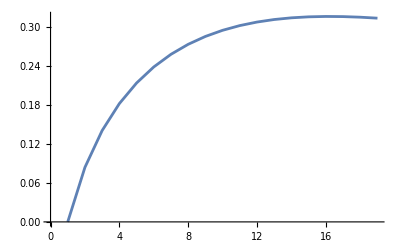

```mathematica
i=60;
ListLinePlot[Table[(TG01al1[[j,i,2]]/Sqrt[TG01al1[[j,i,1]]]-TG01al1[[2,i,2]]/Sqrt[TG01al1[[2,i,1]]])/j^0.5,{j,2,20}]]
```

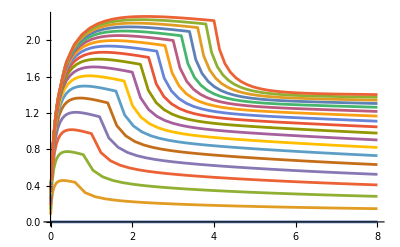

```mathematica
ListLinePlot[Table[{TG01al1[[j,i,1]],TG01al1[[j,i,2]]/Sqrt[TG01al1[[j,i,1]]]-TG01al1[[2,i,2]]/Sqrt[TG01al1[[2,i,1]]]},{j,2,20},{i,1,60}]]
```

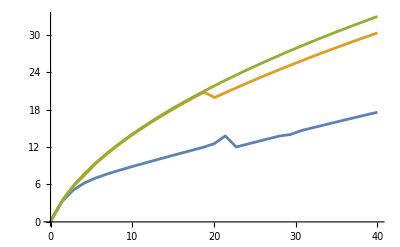

```mathematica
ListLinePlot[TG1al1[[1;;3]]]
```

```mathematica
Timing[Quiet[NIntegrate[2int[10,0.15,p,1,1,a,b],{p,0,Pi/2},{a,-20,20},{b,0,20},AccuracyGoal->8,PrecisionGoal->8]]]
```

{65.7031,14.0709}

```mathematica
Timing[Quiet[NIntegrate[2int[10,0.15,p,1,1,a,b],{p,0,Pi/2},{a,-20,30},{b,0,20},AccuracyGoal->8,PrecisionGoal->8]]]
```

{77.8125,14.0709}

```mathematica
Timing[Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-30,30},{b,0,20},AccuracyGoal->8,PrecisionGoal->8]]]
```

{107.609,8.25571}

```mathematica
Timing[Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-20,30},{b,0,20},AccuracyGoal->8,PrecisionGoal->8]]]
```

{60.4531,13.7912}

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-20,30},{b,0,20},AccuracyGoal->6,PrecisionGoal->6]]
```

13.7912

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-10,30},{b,0,20},AccuracyGoal->5,PrecisionGoal->5]]
```

11.0676

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-30,30},{b,0,20},AccuracyGoal->5,PrecisionGoal->5]]
```

$Aborted

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-30,30},{b,0,20},AccuracyGoal->5,PrecisionGoal->5]]
```

7.21472

```mathematica
curacc[10,0.05,1,1]
```

8.86652

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-20,20},{b,0,20},AccuracyGoal->10,PrecisionGoal->10]]
```

8.86652

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-20,20},{b,0,20},AccuracyGoal->8,PrecisionGoal->8]]
```

8.86652

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-20,20},{b,0,20},AccuracyGoal->5,PrecisionGoal->5]]
```

7.79139

```mathematica
Quiet[NIntegrate[2int[10,0.05,p,1,1,a,b],{p,0,Pi/2},{a,-1,30},{b,0,20},AccuracyGoal->5,PrecisionGoal->5]]
```

13.7789

General::munfl: Internal`AbsSquare[-2.14889×10^-246] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

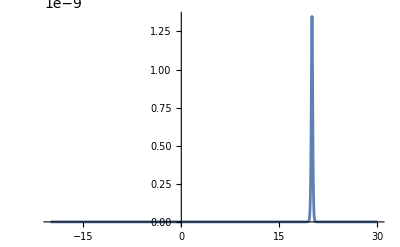

```mathematica
Plot[int[10,0.05,0,1,1,a,20],{a,-20,30},PlotLegends->Automatic,PlotRange->All]
```

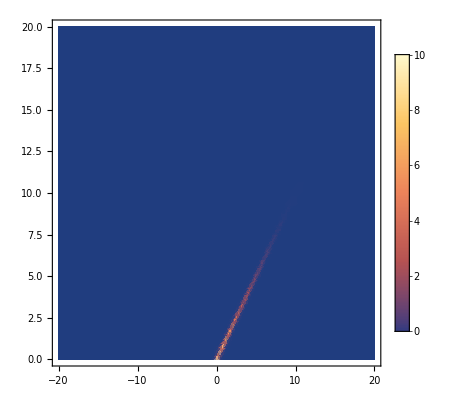

```mathematica
DensityPlot[int[10,0.05,0,1,1,a,b],{a,-20,20},{b,0,20},PlotLegends->Automatic,PlotRange->All,PlotPoints->50]
```

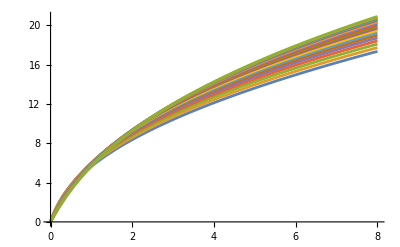

```mathematica
ListLinePlot[TG01al1[[3;;20]]]
```

```mathematica
TG1al1
```

```mathematica
TG1al1={{{0.0014000000000000002,0.004333521514917172},{0.0018000000000000004,0.00557165472143854},{0.0022000000000000006,0.006809773959054634},{0.0026000000000000007,0.00804787910736805},{0.0030000000000000005,0.009285966488478958},{0.0034000000000000007,0.010524033156831184},{0.003800000000000001,0.011762078192667353},{0.004200000000000001,0.013000096108843364},{0.004600000000000002,0.014238085313877734},{0.005000000000000001,0.015476047714663843},{0.009750000000000002,0.030173456986793752},{0.014500000000000002,0.04486171193370687},{0.019250000000000003,0.0595367256799572},{0.024000000000000004,0.07419478322504822},{0.028750000000000005,0.0888325699039095},{0.0335,0.10344717436954246},{0.038250000000000006,0.11803606431679978},{0.04300000000000001,0.13259706036033483},{0.047750000000000015,0.1471282967833206},{0.052500000000000005,0.16162819149108906},{0.05725000000000001,0.17609540741193336},{0.06200000000000001,0.19052882337594926},{0.06675000000000002,0.20492750627548115},{0.07150000000000001,0.2192906862014025},{0.07625000000000001,0.23361773340867878},{0.08100000000000002,0.2479081450299944},{0.08575000000000002,0.2621615182016499},{0.09050000000000002,0.276377546170029},{0.09525000000000002,0.2905560005746255},{0.10000000000000002,0.30469672242469764},{1.43,3.3005065942935476},{2.76,5.083117618986111},{4.089999999999999,6.196590203379132},{5.419999999999999,6.978522763056431},{6.749999999999999,7.5972939641887205},{8.079999999999998,8.144161306127824},{9.409999999999998,8.649257785829494},{10.739999999999998,9.144573184423106},{12.069999999999999,9.626986380234523},{13.399999999999999,10.104319187508366},{14.729999999999999,10.577529426541108},{16.06,11.046203687743215},{17.39,11.509425394030108},{18.72,11.966150324597344},{20.05,12.553257800773688},{21.38,13.787657026573516},{22.709999999999997,12.009861245710635},{24.04,12.45327516592927},{25.369999999999997,12.895071236798204},{26.7,13.334840100352226},{28.029999999999998,13.772323073194558},{29.36,14.009535795819822},{30.689999999999998,14.63951409875058},{32.019999999999996,15.068909856800945},{33.349999999999994,15.495348142814919},{34.68,15.918746054649652},{36.01,16.33904763392377},{37.339999999999996,16.756195846925685},{38.669999999999995,17.170154430120398},{40.,17.580896604656637}},{{0.0019000000000000002,0.005800103823413177},{0.0028000000000000004,0.008547482601847227},{0.0037000000000000006,0.011294817027871443},{0.004600000000000001,0.014042092460077515},{0.0055000000000000005,0.01678929461396574},{0.006400000000000001,0.019536409281901455},{0.007300000000000002,0.02228342219408673},{0.008200000000000002,0.025030319301819592},{0.0091,0.027777086315900364},{0.010000000000000002,0.03052370920221606},{0.019500000000000003,0.05950350885751888},{0.029000000000000005,0.08844978552942814},{0.038500000000000006,0.11734781560264408},{0.04800000000000001,0.146184416373051},{0.05750000000000001,0.17494805823155413},{0.067,0.20362883956545358},{0.07650000000000001,0.23221838213391627},{0.08600000000000002,0.2607096863427105},{0.09550000000000003,0.2890969736938983},{0.10500000000000001,0.31737553187763806},{0.11450000000000002,0.34554157054633045},{0.12400000000000003,0.37359209089217593},{0.13350000000000004,0.40152477095081857},{0.14300000000000002,0.42933786687477293},{0.15250000000000002,0.4570301229459674},{0.16200000000000003,0.4846007012990251},{0.17150000000000004,0.5120491159224491},{0.18100000000000005,0.539375179134704},{0.19050000000000003,0.5665789552589627},{0.20000000000000004,0.5936607209355361},{1.5266666666666666,3.5886713659673766},{2.8533333333333335,5.7956091193915045},{4.18,7.505806572349348},{5.506666666666667,9.327807578644311},{6.833333333333333,10.816236219756036},{8.16,12.185703323437085},{9.486666666666666,13.463220461441688},{10.813333333333333,14.663824699680776},{12.139999999999999,15.800559765570412},{13.466666666666665,16.882766103801824},{14.793333333333333,17.917691127141854},{16.12,18.911098953409308},{17.446666666666665,19.86766078051285},{18.773333333333333,20.791283728612115},{20.099999999999998,19.937489169404852},{21.426666666666666,20.73156201086633},{22.753333333333334,21.506497642221},{24.08,22.26369619758835},{25.406666666666666,23.00437110037575},{26.73333333333333,23.729581215841897},{28.06,24.440257523751235},{29.386666666666667,25.137223404667193},{30.71333333333333,25.82120966158532},{32.04,26.492870129618055},{33.36666666666667,27.152790320106387},{34.693333333333335,27.801492818319826},{36.02,28.43946442381536},{37.34666666666667,29.067122498543462},{38.67333333333334,29.68486333405747},{40.,30.293044134514318}},{{0.0024000000000000002,0.007231091539780748},{0.0038000000000000004,0.011449162638950149},{0.005200000000000001,0.015667142577557892},{0.006600000000000001,0.019884998551671366},{0.008,0.024102697085395326},{0.009400000000000002,0.028320205444779385},{0.0108,0.03253749025638765},{0.012200000000000003,0.03675451853906708},{0.013600000000000001,0.04097125750819451},{0.015000000000000003,0.045187674400898103},{0.029250000000000005,0.08807902254929771},{0.04350000000000001,0.13090068895258175},{0.05775000000000001,0.17362246422553798},{0.07200000000000001,0.2162176704004289},{0.08625000000000001,0.2586633608896843},{0.10050000000000002,0.30094021103344676},{0.11475000000000002,0.3430322328119287},{0.12900000000000003,0.38492641270090033},{0.14325000000000004,0.42661233289979406},{0.15750000000000003,0.46808180769940444},{0.17175000000000004,0.5093285526531375},{0.18600000000000005,0.5503478900661217},{0.20025000000000004,0.5911364953913244},{0.21450000000000005,0.6316921771042096},{0.22875000000000004,0.6720136911677672},{0.24300000000000005,0.7121005822002475},{0.25725000000000003,0.7519530502865196},{0.2715000000000001,0.7915718380821587},{0.28575000000000006,0.8309581361278452},{0.30000000000000004,0.8701135028308518},{1.6233333333333335,3.811164873247897},{2.946666666666667,6.027409608874934},{4.2700000000000005,7.891261626055591},{5.593333333333334,9.534248199917412},{6.916666666666667,11.02144491537728},{8.240000000000002,12.390887054063986},{9.563333333333334,13.667155264385782},{10.886666666666668,14.86725105814284},{12.210000000000003,16.003526903100834},{13.533333333333335,17.085299141195108},{14.85666666666667,18.119803395429766},{16.180000000000003,19.112795351075984},{17.503333333333337,20.068942375471252},{18.826666666666668,20.992092210929847},{20.150000000000002,21.88546056423773},{21.473333333333336,22.751766059882087},{22.79666666666667,23.593330437524337},{24.120000000000005,24.412152156627588},{25.443333333333335,25.20996578118723},{26.76666666666667,25.988284889281957},{28.090000000000003,26.748436656100942},{29.413333333333338,27.49159318019919},{30.73666666666667,28.218792124354508},{32.06,28.930954834945187},{33.38333333333333,29.628908354994905},{34.70666666666667,30.313387332810272},{36.03,30.98505619445161},{37.35333333333333,31.644512694778342},{38.67666666666667,32.29229758810234},{40.,32.92890185460617}},{{0.0029000000000000007,0.008629698564225855},{0.0048000000000000004,0.014283539384832218},{0.006700000000000001,0.019937232512859226},{0.008600000000000002,0.02559071950597343},{0.010500000000000002,0.031243942149230205},{0.012400000000000001,0.036896842427431784},{0.014300000000000004,0.042549362317644786},{0.016200000000000003,0.04820144407095957},{0.018100000000000005,0.0538530302275757},{0.020000000000000004,0.05950406356759736},{0.03900000000000001,0.11597164571878743},{0.05800000000000001,0.1723239229781693},{0.07700000000000001,0.22851148744384425},{0.09600000000000002,0.28449123152037803},{0.11500000000000002,0.34022661671349275},{0.134,0.3956873907989459},{0.15300000000000002,0.45084901447786757},{0.17200000000000004,0.5056919732699598},{0.19100000000000006,0.5602010784370256},{0.21000000000000002,0.6143648129939607},{0.22900000000000004,0.6681747445436328},{0.24800000000000005,0.7216250148132366},{0.26700000000000007,0.7747119012662828},{0.28600000000000003,0.8274334445465785},{0.30500000000000005,0.8797891375095833},{0.32400000000000007,0.9317796622549248},{0.3430000000000001,0.983406671132612},{0.3620000000000001,1.0346726044638779},{0.38100000000000006,1.0855805383070651},{0.4000000000000001,1.1361340577236996},{1.7200000000000002,4.025829015444533},{3.04,6.231791221352556},{4.36,8.092122465485962},{5.680000000000001,9.733591817218066},{7.000000000000001,11.220028652975039},{8.32,12.589032362622621},{9.64,13.865003937808181},{10.96,15.064863404129765},{12.280000000000001,16.200923823549406},{13.600000000000001,17.28248191952863},{14.920000000000002,18.316764010576893},{16.24,19.309520750366442},{17.56,20.26541778656353},{18.88,21.188302219996274},{20.2,22.08138965259595},{21.52,22.9473989101386},{22.84,23.788651905985997},{24.16,24.607147238100683},{25.48,25.40461855583771},{26.8,26.182579016845494},{28.12,26.94235610543115},{29.44,27.685120725192274},{30.76,28.411909347893907},{32.08,29.12364371160756},{33.4,29.82114726582991},{34.72,30.505155898334113},{36.04,31.176332636472544},{37.36,31.835273709114833},{38.68,32.48252156562175},{40.,33.11856434256122}},{{0.0034000000000000002,0.009998603579606101},{0.0058000000000000005,0.017056306250329018},{0.0082,0.024113792315007522},{0.010600000000000002,0.031170973570880157},{0.013000000000000001,0.03822777097013679},{0.0154,0.04528408620264358},{0.017800000000000003,0.05233983528754831},{0.020200000000000003,0.059394930222869444},{0.022600000000000002,0.06644928424023025},{0.025,0.07350281091836976},{0.04875,0.1432406177034956},{0.07250000000000001,0.2128097054955813},{0.09625,0.2821385457539921},{0.12,0.3511654089431751},{0.14375,0.419838653221303},{0.1675,0.4881161692466241},{0.19125,0.5559644018092329},{0.215,0.6233572292220073},{0.23875,0.6902748535512468},{0.2625,0.756702781020559},{0.28625,0.822630922432293},{0.31000000000000005,0.8880528201306774},{0.33375000000000005,0.9529649923816124},{0.35750000000000004,1.0173663842274652},{0.38125000000000003,1.0812579099442725},{0.405,1.1446420734870297},{0.42875,1.2075226540788242},{0.4525,1.26990444766838},{0.47625,1.3317930522160841},{0.5,1.393194690952522},{1.8166666666666667,4.234106413812058},{3.1333333333333333,6.4293977682557},{4.45,8.286236431783344},{5.766666666666667,9.926381443730426},{7.083333333333333,11.412302001948456},{8.4,12.781117035743296},{9.716666666666667,14.057031689275265},{11.033333333333333,15.256878690715833},{12.35,16.39293050047328},{13.666666666666666,17.474465000071106},{14.983333333333333,18.508699908584056},{16.3,19.50138270465313},{17.616666666666667,20.457178470614096},{18.933333333333334,21.379935082103557},{20.25,22.27286839065945},{21.566666666666666,23.13869993836029},{22.883333333333333,23.97975104312032},{24.2,24.798021616632546},{25.516666666666666,25.595245909961914},{26.833333333333332,26.372936791250286},{28.15,27.13242191435583},{29.466666666666665,27.874871383536867},{30.78333333333333,28.601321689273888},{32.1,29.312694026059184},{33.416666666666664,30.009810490036696},{34.733333333333334,30.693407400379943},{36.05,31.36414646113997},{37.36666666666667,32.022624247940726},{38.68333333333333,32.66938069615101},{40.,33.30490541359217}},{{0.0039000000000000007,0.011340085979842034},{0.006800000000000001,0.019772280350045805},{0.009700000000000004,0.02820418627865194},{0.012600000000000004,0.03663568105644223},{0.015500000000000003,0.045066642164998734},{0.018400000000000007,0.053496947772665435},{0.021300000000000006,0.06192647583956185},{0.024200000000000006,0.0703551053633227},{0.027100000000000006,0.07878271566432811},{0.030000000000000006,0.08720918691307597},{0.05850000000000001,0.16993586428683902},{0.08700000000000002,0.2524338639394927},{0.11550000000000002,0.33460719087477037},{0.14400000000000002,0.41637382591384586},{0.17250000000000001,0.4976659685587343},{0.20100000000000004,0.5784290960225843},{0.22950000000000004,0.658620466620231},{0.25800000000000006,0.7382074629529918},{0.2865000000000001,0.8171659891690201},{0.31500000000000006,0.8954790222412978},{0.3435000000000001,0.9731353508673946},{0.3720000000000001,1.0501285036597823},{0.4005000000000001,1.126455851156258},{0.4290000000000001,1.2021178599098266},{0.4575000000000001,1.2771174772460894},{0.4860000000000001,1.3514596253318096},{0.5145000000000001,1.425150785461139},{0.5430000000000001,1.4981986589491647},{0.5715000000000001,1.5706118881020905},{0.6000000000000001,1.6423998302953282},{1.9133333333333333,4.436879029485869},{3.2266666666666666,6.621006711528854},{4.539999999999999,8.474216929148023},{5.8533333333333335,10.113100459462666},{7.166666666666666,11.59865013103319},{8.479999999999999,12.967452821604278},{9.793333333333333,14.24349421183179},{11.106666666666666,15.443509238651199},{12.419999999999998,16.579725158381947},{13.733333333333333,17.66139883971555},{15.046666666666665,18.695739253819784},{16.36,19.688490864571513},{17.673333333333332,20.644318552051654},{18.986666666666668,21.567071495722484},{20.3,22.459967864300502},{21.613333333333333,23.325729542132475},{22.926666666666666,24.16668015373072},{24.24,24.984820985420487},{25.553333333333335,25.781886744880854},{26.866666666666667,26.559391059437964},{28.18,27.31866164621265},{29.493333333333332,28.060868787396384},{30.806666666666665,28.78704857507744},{32.12,29.49812207422702},{33.43333333333333,30.19491097324311},{34.74666666666666,30.878151244313322},{36.06,31.548504176926066},{37.373333333333335,32.20656612918462},{38.68666666666667,32.852876380787585},{40.,33.487924901851734}},{{0.0044,0.012656106676795665},{0.0078000000000000005,0.02243560455546681},{0.011200000000000002,0.03221473283690006},{0.014600000000000002,0.041993330841175305},{0.018000000000000002,0.051771238185131255},{0.021400000000000002,0.06154829508172329},{0.024800000000000003,0.07132434218074761},{0.028200000000000003,0.08109922099999259},{0.0316,0.09087277376898575},{0.035,0.1006448436110383},{0.06825,0.1961001053729444},{0.1015,0.29126113991135144},{0.13475,0.38600557529069823},{0.168,0.4802298200525218},{0.20125,0.5738491816615423},{0.23450000000000001,0.6667964227271617},{0.26775000000000004,0.7590196311966728},{0.30100000000000005,0.8504799343427247},{0.33425000000000005,0.9411493273085542},{0.36750000000000005,1.031008739142739},{0.40075000000000005,1.1200463709804416},{0.43400000000000005,1.2082562967033499},{0.46725000000000005,1.2956373020242735},{0.5005000000000001,1.3821919292130225},{0.5337500000000001,1.467925694615842},{0.5670000000000001,1.5528464507175717},{0.6002500000000001,1.6369638668927733},{0.6335000000000001,1.7202890072526187},{0.6667500000000001,1.802833987682752},{0.7000000000000001,1.884611700384125},{2.01,4.634809662949102},{3.32,6.807263183612862},{4.63,8.656603653782968},{5.9399999999999995,10.294188321459039},{7.249999999999999,11.779432213437905},{8.559999999999999,13.148335915697393},{9.869999999999997,14.424638365844755},{11.179999999999998,15.624962721689847},{12.489999999999998,16.76148371426475},{13.799999999999997,17.843433818226735},{15.109999999999998,18.87801129526399},{16.419999999999998,19.870956786047458},{17.729999999999997,20.826934967848242},{19.039999999999996,21.7497960221399},{20.349999999999998,22.642760246607782},{21.659999999999997,23.50855135163346},{22.969999999999995,24.34949515607336},{24.279999999999998,25.16759406808485},{25.589999999999996,25.964583520484474},{26.899999999999995,26.74197855785059},{28.209999999999997,27.501107151273757},{29.519999999999996,28.243139867182077},{30.829999999999995,28.969112874570943},{32.14,29.679947096715416},{33.449999999999996,30.376464162329032},{34.76,31.059399779206807},{36.07,31.72941511523078},{37.379999999999995,32.3871065001107},{38.69,33.03301277470759},{40.,33.66762436072604}},{{0.004900000000000001,0.013948375562719812},{0.008800000000000002,0.02504987652599933},{0.012700000000000003,0.03615092071038712},{0.016600000000000004,0.04725130601222902},{0.020500000000000004,0.05835083136202565},{0.024400000000000005,0.06944929567407976},{0.028300000000000006,0.08054649910109535},{0.032200000000000006,0.09164224258874984},{0.03610000000000001,0.10273632823848956},{0.04000000000000001,0.11382855932274107},{0.07800000000000001,0.2217703504903154},{0.11600000000000002,0.32934752291643743},{0.15400000000000003,0.43640975000014337},{0.19200000000000003,0.5428308785028562},{0.23000000000000004,0.6485088253487474},{0.268,0.7533635147083636},{0.30600000000000005,0.8573340049996492},{0.3440000000000001,0.9603754837696704},{0.3820000000000001,1.062456462819487},{0.42000000000000004,1.163556310377679},{0.4580000000000001,1.2636631547979882},{0.4960000000000001,1.3627721363669494},{0.5340000000000001,1.4608839665677187},{0.5720000000000001,1.5580037554184551},{0.6100000000000001,1.654140055191121},{0.6480000000000001,1.7493040886890086},{0.6860000000000002,1.8435091239966535},{0.7240000000000002,1.93676996835383},{0.7620000000000001,2.0291025646650924},{0.8000000000000002,2.1205236628228543},{2.1066666666666665,4.828414592483614},{3.413333333333333,6.988708363010277},{4.72,8.833872034638652},{6.026666666666666,10.470045570869624},{7.333333333333333,11.954983452656458},{8.64,13.324047915265762},{9.946666666666667,14.600702223060894},{11.253333333333334,15.801441807208718},{12.56,16.938380044247232},{13.866666666666667,18.020719877019403},{15.173333333333334,19.05564601027428},{16.48,20.048893692553914},{17.786666666666665,21.005126439517664},{19.093333333333334,21.928195270734328},{20.400000000000002,22.821322185868254},{21.706666666666667,23.687232801774535},{23.013333333333332,24.528254710746385},{24.32,25.346391852811},{25.62666666666667,26.14338154825621},{26.933333333333334,26.920738986806004},{28.24,27.679793029435885},{29.546666666666667,28.421714662816903},{30.853333333333335,29.14754030344743},{32.16,29.858190997174187},{33.46666666666666,30.554488249960695},{34.773333333333326,31.237167986718347},{36.08,31.90689116029458},{37.38666666666666,32.56425439728328},{38.69333333333333,33.2097963595542},{40.,33.844007575741436}},{{0.0054,0.015218396056734071},{0.0098,0.02761825458114072},{0.0142,0.0400175637068743},{0.018600000000000002,0.052416077659489156},{0.023000000000000003,0.06481355062518561},{0.0274,0.07720973845637047},{0.0318,0.0896043975398794},{0.0362,0.10199728566233313},{0.040600000000000004,0.11438816181469857},{0.045000000000000005,0.12677678678975707},{0.08775000000000001,0.24697899518702243},{0.1305,0.3667419493656253},{0.17325000000000002,0.4858860549721905},{0.21600000000000003,0.6042618295125568},{0.25875000000000004,0.7217494783079713},{0.3015,0.8382560899344063},{0.34425,0.9537119158155271},{0.387,1.068066565956635},{0.42975,1.1812855066196626},{0.47250000000000003,1.2933470235719862},{0.5152500000000001,1.4042396604536915},{0.558,1.513960101801226},{0.6007500000000001,1.6225114472581281},{0.6435000000000001,1.7299018099509795},{0.6862500000000001,1.836143186193168},{0.7290000000000001,1.9412505452423454},{0.77175,2.0452410999416846},{0.8145000000000001,2.1481337228007438},{0.8572500000000001,2.2499484718999643},{0.9000000000000001,2.3507062226887196},{2.2033333333333336,5.018106286530824},{3.506666666666667,7.1658005565415195},{4.8100000000000005,9.00644295614961},{6.113333333333334,10.641037840826773},{7.416666666666668,12.12561678537181},{8.72,13.494856244099271},{10.023333333333335,14.771915110901567},{11.326666666666668,15.97314414574291},{12.63,17.110585308526197},{13.933333333333335,18.193405987100284},{15.236666666666668,19.228773656287803},{16.54,20.222415924851628},{17.843333333333334,21.178993706540375},{19.14666666666667,22.102358062307022},{20.45,22.995732194225035},{21.753333333333334,23.86184330965532},{23.05666666666667,24.703020736463678},{24.36,25.521270681804694},{25.663333333333334,26.318329155324356},{26.96666666666667,27.09571487020425},{28.27,27.854756599950253},{29.573333333333334,28.596625790746632},{30.87666666666667,29.3223591864105},{32.18,30.032877926235614},{33.483333333333334,30.72900393024699},{34.78666666666667,31.411473054219115},{36.09,32.08094654072292},{37.39333333333334,32.73802073304761},{38.696666666666665,33.383235357345384},{40.,34.017080558453564}},{{0.005900000000000001,0.01646750226225831},{0.0108,0.0301435349179003},{0.015700000000000002,0.04381892131086634},{0.020600000000000004,0.05749336818096633},{0.025500000000000005,0.07116658385502982},{0.030400000000000003,0.08483827749691708},{0.035300000000000005,0.09850815965962569},{0.04020000000000001,0.11217594236947993},{0.04510000000000001,0.12584133929876798},{0.05000000000000001,0.13950406626865622},{0.0975,0.2717546489331774},{0.14500000000000002,0.4034875818934687},{0.1925,0.5344929025800279},{0.24,0.664597208685001},{0.2875,0.7936628056828183},{0.335,0.9215840420401692},{0.3825,1.0482826413571176},{0.43,1.1737030196327343},{0.4775,1.2978080404657917},{0.525,1.4205753664050103},{0.5725,1.5419944121257987},{0.6200000000000001,1.6620638489112964},{0.6675000000000001,1.7807895785370145},{0.7150000000000001,1.8981831033577705},{0.7625000000000001,2.0142602178408437},{0.81,2.129039964398543},{0.8575,2.2425437965866504},{0.905,2.354794916315539},{0.9525,2.465817741401092},{1.,2.57563748898668},{2.3,5.2042214250086305},{3.6,7.338930140989576},{4.9,9.174690239612623},{6.2,10.80749927879008},{7.5,12.291624302267971},{8.8,13.661014706884574},{10.1,14.938497604182519},{11.4,16.14026195552014},{12.700000000000001,17.2782676404532},{14.,18.361639751723526},{15.3,19.397524308091967},{16.6,20.39163845622361},{17.900000000000002,21.348638805600434},{19.2,22.2723750854376},{20.5,23.16607093967822},{21.8,24.032454734872125},{23.1,24.87385666429003},{24.400000000000002,25.692284640067843},{25.7,26.4894769652543},{27.,27.26695125455094},{28.3,28.026037690936516},{29.6,28.76790828138042},{30.900000000000002,29.493600142900526},{32.2,30.20403474424018},{33.5,30.900034201950128},{34.800000000000004,31.582334548375613},{36.1,32.251597342834664},{37.4,32.908419204033486},{38.7,33.553340189165176},{40.,34.186850830733874}},{{0.006400000000000001,0.01769688496416069},{0.011800000000000001,0.03262821143203397},{0.017200000000000003,0.047558789423565874},{0.022600000000000006,0.0624882773824711},{0.028000000000000008,0.07741633458496544},{0.033400000000000006,0.0923426218238485},{0.03880000000000001,0.10726680119709288},{0.04420000000000001,0.12218853695405765},{0.04960000000000001,0.13710749524332935},{0.055000000000000014,0.15202334479680654},{0.10725000000000001,0.2961227677520893},{0.15950000000000003,0.439622786539928},{0.21175,0.5822821399029414},{0.264,0.7239030555933579},{0.31625000000000003,0.8643298545559764},{0.3685,1.0034443093356482},{0.42075,1.1411599295865822},{0.47300000000000003,1.2774163364663285},{0.5252500000000001,1.4121742240053434},{0.5775000000000001,1.5454110708023088},{0.6297500000000001,1.6771175904238071},{0.682,1.8072948426830426},{0.7342500000000001,1.935951905206269},{0.7865000000000001,2.06310401347714},{0.8387500000000001,2.1887710713616526},{0.8910000000000001,2.3129764741635923},{0.9432500000000001,2.4357461684615127},{0.9955000000000002,2.5571079110813475},{1.0477500000000002,2.677090679985281},{1.1,2.795724212996581},{2.3966666666666665,5.387039929953534},{3.6933333333333334,7.508433867619697},{4.99,9.338946921117335},{6.286666666666667,10.969735534358726},{7.583333333333334,12.453278580925597},{8.879999999999999,13.82276388426218},{10.176666666666666,15.100661487373696},{11.473333333333333,16.302981817171453},{12.77,17.44159178791309},{14.066666666666666,18.525567094994674},{15.363333333333333,19.562027488115117},{16.66,20.556676640211187},{17.956666666666667,21.514164511651654},{19.253333333333334,22.43833825672609},{20.55,23.332420790162306},{21.846666666666668,24.19914088199389},{23.143333333333334,25.04082954470399},{24.44,25.859495511024157},{25.736666666666668,26.656878045656487},{27.033333333333335,27.434495434093357},{28.330000000000002,28.19367843566609},{29.62666666666667,28.935599526133533},{30.923333333333336,29.66129614314085},{32.22,30.37169018240286},{33.516666666666666,31.067603937716296},{34.81333333333333,31.749773843734136},{36.11,32.418861723587725},{37.406666666666666,33.075464577384444},{38.70333333333333,33.72012293354941},{40.,34.35332780101752}},{{0.006900000000000002,0.018907615069430696},{0.012800000000000002,0.035074520621659486},{0.018700000000000005,0.05124057293308244},{0.024600000000000007,0.06740537816121103},{0.03050000000000001,0.08356854432675612},{0.03640000000000001,0.09972968247654602},{0.04230000000000001,0.11588840423148715},{0.048200000000000014,0.1320443237624163},{0.054100000000000016,0.14819705798392005},{0.06000000000000002,0.16434622620076517},{0.11700000000000002,0.3201061549908262},{0.17400000000000004,0.47518189845769454},{0.23100000000000004,0.6293001088881112},{0.28800000000000003,0.782238306677643},{0.34500000000000003,0.9338228250228147},{0.4020000000000001,1.0839230727438642},{0.4590000000000001,1.2324446864243968},{0.5160000000000001,1.3793228938020592},{0.5730000000000002,1.5245166420097316},{0.6300000000000001,1.6680036434638923},{0.6870000000000002,1.8097763078055007},{0.7440000000000002,1.9498384521570715},{0.8010000000000002,2.0882026688266935},{0.8580000000000002,2.2248882287648986},{0.9150000000000001,2.3599194209609466},{0.9720000000000002,2.4933242356289043},{1.0290000000000001,2.625133328662443},{1.0860000000000003,2.7553792024749697},{1.1430000000000002,2.884095563506776},{1.2000000000000002,3.0113168162594963},{2.493333333333333,5.566798277840653},{3.7866666666666666,7.674600366671186},{5.08,9.499510498127913},{6.373333333333333,11.128026412949207},{7.666666666666666,12.610833887861695},{8.96,13.980331570901411},{10.253333333333334,15.258609772597957},{11.546666666666667,16.461484451618524},{12.84,17.600718743966375},{14.133333333333333,18.68533165425298},{15.426666666666666,19.722411396464246},{16.72,20.717645583215436},{18.013333333333332,21.675674259827876},{19.306666666666665,22.60034052071858},{20.599999999999998,23.49486538082983},{21.89333333333333,24.361977050122277},{23.186666666666664,25.20400710457968},{24.479999999999997,26.02296351891866},{25.77333333333333,26.82058725420658},{27.066666666666663,27.59839653394697},{28.359999999999996,28.35772276227905},{29.65333333333333,29.099738453961127},{30.946666666666662,29.825481914969703},{32.24,30.535874805812362},{33.53333333333333,31.23173995436481},{34.82666666666667,31.913814070900152},{36.12,32.58275944177335},{37.413333333333334,33.23917346145981},{38.70666666666666,33.883597187083865},{40.,34.51652230830076}},{{0.0074,0.02010066133612957},{0.0138,0.03748448447691561},{0.020200000000000003,0.05486734352112717},{0.026600000000000002,0.07224879395009003},{0.033,0.08962839034930652},{0.039400000000000004,0.10700569094402161},{0.0458,0.12438025635553537},{0.0522,0.14175164850910105},{0.058600000000000006,0.15911943073979906},{0.065,0.17648317122416565},{0.12675,0.3437253566701021},{0.1885,0.5101958295882166},{0.25025,0.6755884855974921},{0.312,0.8396558933501769},{0.37374999999999997,1.002206456902516},{0.4355,1.1630974744643254},{0.49725,1.3222270624536747},{0.5589999999999999,1.4795264561099812},{0.6207499999999999,1.634953264842404},{0.6824999999999999,1.788485830498829},{0.7442500000000001,1.9401186290772525},{0.806,2.089858571682024},{0.86775,2.2377220718204223},{0.9295,2.3837327095399106},{0.99125,2.5279193965324667},{1.053,2.670314931926312},{1.11475,2.810954865476002},{1.1764999999999999,2.9498766075718},{1.2382499999999999,3.087118732354291},{1.2999999999999998,3.222720435003075},{2.59,5.743699024607079},{3.88,7.837689506381509},{5.17,9.656647421702305},{6.46,11.28262824655978},{7.75,12.764527309707919},{9.040000000000001,14.133933238354293},{10.330000000000002,15.41253674938272},{11.620000000000001,16.615944535066145},{12.91,17.75580549236695},{14.200000000000001,18.84107460506426},{15.490000000000002,19.87880404477055},{16.78,20.874659903582938},{18.07,21.833271544227607},{19.360000000000003,22.75847541810604},{20.650000000000002,23.65348930068694},{21.94,24.521039772492305},{23.23,25.363457440577328},{24.52,26.182751181035265},{25.810000000000002,26.98066088656036},{27.1,27.758705457258806},{28.39,28.518216118533516},{29.680000000000003,29.2603662188257},{30.970000000000002,29.986193771492875},{32.26,30.6966208170183},{33.55,31.39247052441727},{34.839999999999996,32.07447990054413},{36.129999999999995,32.74331165840228},{37.42,33.39956378823314},{38.71,34.04377785610035},{40.,34.67644637448106}},{{0.0079,0.021276900674109468},{0.0148,0.03985993264577291},{0.021700000000000004,0.05844188803993232},{0.028600000000000004,0.07702226644634697},{0.035500000000000004,0.0956005688711701},{0.04240000000000001,0.11417629868987601},{0.049300000000000004,0.13274896180825851},{0.05620000000000001,0.1513180671626514},{0.0631,0.1698831271383729},{0.07,0.1884436584655054},{0.1365,0.3669989815370748},{0.203,0.544692557836217},{0.2695,0.7211849550797694},{0.336,0.8962036205019801},{0.4025,1.0695391383708945},{0.46900000000000003,1.2410369816923137},{0.5355000000000001,1.410588102426146},{0.6020000000000001,1.578120142079069},{0.6685000000000001,1.7435897658832775},{0.7350000000000001,1.906976319546327},{0.8015000000000001,2.0682766881052324},{0.8680000000000001,2.227501192365705},{0.9345000000000001,2.384670338848341},{1.0010000000000001,2.5398122614936316},{1.0675000000000001,2.6929607066217476},{1.1340000000000001,2.8441534713027536},{1.2005000000000001,2.993431153432152},{1.2670000000000001,3.1408362114400483},{1.3335000000000001,3.2864122046647797},{1.4000000000000001,3.4302032182770685},{2.6866666666666665,5.917917800101046},{3.9733333333333336,7.997916634739992},{5.26,9.810596880163517},{6.546666666666667,11.433776045155026},{7.833333333333334,12.914579927747946},{9.12,14.283772494746882},{10.406666666666666,15.562628080065982},{11.693333333333333,16.76653059229629},{12.98,17.907004721898534},{14.266666666666667,18.992933767046637},{15.553333333333333,20.031329875222383},{16.84,21.02783328527413},{18.126666666666665,21.987059526886476},{19.41333333333333,22.912836670056155},{20.7,23.808377658961753},{21.986666666666665,24.67640637928244},{23.27333333333333,25.519252234113583},{24.56,26.338922173523812},{25.846666666666664,27.13715677610069},{27.133333333333333,27.915474274546},{28.419999999999998,28.675205928700258},{29.706666666666663,29.41752504778095},{30.993333333333332,30.143469565500645},{32.28,30.853961688073245},{33.56666666666666,31.54982511934323},{34.85333333333333,32.23179711336495},{36.14,32.90054071715307},{37.42666666666666,33.55665463122528},{38.71333333333333,34.200681092847944},{40.,34.833113119404096}},{{0.008400000000000001,0.022437136722585446},{0.0158,0.04220253564498218},{0.023200000000000005,0.061966741893130985},{0.030600000000000006,0.08172919857198817},{0.038000000000000006,0.10148935070267959},{0.04540000000000001,0.12124664568487346},{0.05280000000000001,0.14100053358606954},{0.06020000000000001,0.16075046854859587},{0.06760000000000001,0.1804959085674714},{0.07500000000000001,0.20023631621978027},{0.14625000000000002,0.389943963796223},{0.21750000000000003,0.5786975264632466},{0.28875000000000006,0.7661237586280072},{0.36000000000000004,0.9519248806543332},{0.4312500000000001,1.1358738137596298},{0.5025000000000001,1.3178044847734285},{0.57375,1.4976010690792636},{0.645,1.6751879957498799},{0.71625,1.8505213657816593},{0.7875000000000001,2.023581881059142},{0.8587500000000001,2.1943691583876315},{0.9300000000000002,2.362897211399031},{1.0012500000000002,2.5291908935990075},{1.0725,2.6932831085052733},{1.14375,2.8552126319520386},{1.215,3.0150224083844672},{1.2862500000000001,3.17275823478362},{1.3575000000000002,3.3284677284700934},{1.4287500000000002,3.4821995302924873},{1.5000000000000002,3.634002707923311},{2.783333333333333,6.089608475095881},{4.066666666666666,8.155479395463887},{5.35,9.96157418610228},{6.633333333333333,11.581685422235644},{7.916666666666666,13.061197715369243},{9.2,14.430041538046112},{10.483333333333333,15.709060781068521},{11.766666666666666,16.91340489815719},{13.049999999999999,18.054464637044276},{14.333333333333332,19.141045815908033},{15.616666666666665,20.1801124957543},{16.9,21.177278175005338},{18.18333333333333,22.137140776432297},{19.466666666666665,23.063517812741825},{20.75,23.959615816766807},{22.03333333333333,24.82815464973244},{23.316666666666663,25.67146078749019},{24.599999999999998,26.491540978948528},{25.883333333333333,27.290133366613485},{27.166666666666664,28.0687560172496},{28.449999999999996,28.828739668912743},{29.73333333333333,29.57125762915719},{31.016666666666666,30.297347382983176},{32.3,31.00793176476284},{33.58333333333333,31.703834180448997},{34.86666666666666,32.38579235475056},{36.15,33.05446992845379},{37.43333333333333,33.710465794186426},{38.71666666666666,34.35432330660192},{40.,34.98653589788011}},{{0.008900000000000002,0.023582102481228343},{0.016800000000000006,0.044513820965323976},{0.024700000000000007,0.06544422675195666},{0.03260000000000001,0.08637270579223949},{0.040500000000000015,0.10729864534183532},{0.04840000000000001,0.12822143525101967},{0.05630000000000002,0.14914046903220837},{0.06420000000000002,0.17005514415144266},{0.07210000000000003,0.19096486267147927},{0.08000000000000003,0.21186903184172556},{0.15600000000000003,0.4125757762205089},{0.23200000000000004,0.6122339719604114},{0.30800000000000005,0.8104361452265516},{0.38400000000000006,1.0068592352123247},{0.4600000000000001,1.2012586822670792},{0.536,1.3934571905081565},{0.6120000000000001,1.5833325156720175},{0.6880000000000002,1.7708062586034516},{0.7640000000000002,1.955834317749312},{0.8400000000000001,2.1383990878389003},{0.9160000000000001,2.318503215347882},{0.9920000000000002,2.4961646711196273},{1.0680000000000003,2.6714128835857047},{1.1440000000000001,2.8442857239794295},{1.2200000000000002,3.014827160709355},{1.2960000000000003,3.18308543667984},{1.3720000000000003,3.3491116583543197},{1.4480000000000004,3.51295870498546},{1.5240000000000002,3.674680388280442},{1.6000000000000003,3.8343308057966556},{2.88,6.258907143363871},{4.16,8.31055077698655},{5.4399999999999995,10.10977352288265},{6.720000000000001,11.72655435999141},{8.,13.20457265229333},{9.28,14.572921694682865},{10.56,15.852004120522823},{11.84,17.056723447596518},{13.12,18.198328763547924},{14.4,19.285541036424007},{15.68,20.32527270415233},{16.96,21.323105309755707},{18.240000000000002,22.28361672470274},{19.520000000000003,23.210612657021592},{20.8,24.10728885559682},{22.080000000000002,24.976362480653094},{23.360000000000003,25.820155586475654},{24.64,26.640672502744025},{25.92,27.439649749628078},{27.200000000000003,28.218604289358524},{28.48,28.97886624445907},{29.76,29.72160789128628},{31.040000000000003,30.447866987327508},{32.32,31.15856610285433},{33.6,31.854528757212737},{34.88,32.53649299846529},{36.160000000000004,33.205122835151975},{37.440000000000005,33.861017926968536},{38.72,34.50472202865219},{40.,35.13673009550808}},{{0.009400000000000002,0.024712475872961177},{0.017800000000000007,0.04679519094862306},{0.026200000000000008,0.06887647230188412},{0.03460000000000001,0.0909556454931726},{0.04300000000000002,0.11303203854166118},{0.051400000000000015,0.13510498263834472},{0.05980000000000002,0.15717381271697345},{0.06820000000000002,0.1792378683345278},{0.07660000000000003,0.20129649439143632},{0.08500000000000003,0.22334904177458884},{0.16575000000000004,0.43490861179058854},{0.24650000000000005,0.6453231978060803},{0.32725000000000004,0.8541507442206684},{0.4080000000000001,1.061042903025872},{0.4887500000000001,1.2657378396407948},{0.5695000000000001,1.468047358235355},{0.6502500000000002,1.6678431670193377},{0.7310000000000001,1.8650444055294617},{0.8117500000000002,2.059607119850318},{0.8925000000000001,2.2515157116698057},{0.9732500000000002,2.4407761383566635},{1.0540000000000003,2.627410570169076},{1.1347500000000001,2.8114532194800597},{1.2155000000000002,2.9929471021333325},{1.2962500000000001,3.1719415317337134},{1.3770000000000002,3.348490168078658},{1.4577500000000003,3.5226495378326614},{1.5385000000000002,3.6944778622841863},{1.6192500000000003,3.8640341903840585},{1.7000000000000002,4.031377714712645},{2.9766666666666666,6.42593514480606},{4.253333333333334,8.463284616018454},{5.53,10.25537043697092},{6.806666666666667,11.868564762909157},{8.083333333333332,13.344883585991003},{9.36,14.712583826226696},{10.636666666666667,15.991618311580806},{11.913333333333334,17.196635907109084},{13.190000000000001,18.33873580431098},{14.466666666666665,19.426548051235656},{15.743333333333332,20.466928665964844},{17.02,21.465423512958864},{18.296666666666667,22.42658755469141},{19.57333333333333,23.35421070074079},{20.849999999999998,24.25148134082492},{22.126666666666665,25.121107374487835},{23.403333333333332,25.96540707938732},{24.68,26.786381577689063},{25.956666666666663,27.5857650978807},{27.23333333333333,28.36507292023456},{28.509999999999998,29.12563401845202},{29.786666666666665,29.868619861876052},{31.063333333333333,30.59506774111724},{32.34,31.305899997682214},{33.61666666666667,32.00194017807397},{34.89333333333334,32.68392654222001},{36.17,33.35252352403772},{37.446666666666665,34.008331305719494},{38.723333333333336,34.65189458431573},{40.,35.28370902803312}},{{0.009900000000000003,0.025828876439838278},{0.018800000000000004,0.0490479378403946},{0.027700000000000006,0.07226544079064001},{0.03660000000000001,0.09548065009879542},{0.04550000000000001,0.11869283318529711},{0.05440000000000001,0.1419012612214688},{0.06330000000000001,0.16510520899730535},{0.07220000000000001,0.18830395740413317},{0.08110000000000002,0.21149679271756086},{0.09000000000000002,0.2346829942586717},{0.17550000000000002,0.45695553286817653},{0.261,0.6779848013657005},{0.34650000000000003,0.8972938772831087},{0.43200000000000005,1.114509153755318},{0.5175000000000001,1.3293517521340394},{0.603,1.5416229093008689},{0.6885,1.7511886469935296},{0.774,1.957966004659621},{0.8595,2.1619115091521306},{0.9450000000000001,2.363011868900684},{1.0305000000000002,2.561276613892369},{1.116,2.7567323375505137},{1.2015000000000002,2.9494182288841513},{1.2870000000000001,3.139382609498538},{1.3725000000000003,3.326680266014136},{1.4580000000000002,3.5113703939296124},{1.5435,3.6935150186898618},{1.6290000000000002,3.8731777846794784},{1.7145000000000001,4.050423032545939},{1.8000000000000003,4.225315096809474},{3.0733333333333333,6.590801437057016},{4.346666666666667,8.61381831156949},{5.62,10.398523935794177},{6.8933333333333335,12.007883894554428},{8.166666666666668,13.482297088755539},{9.440000000000001,14.849188814666773},{10.713333333333335,16.128056153288075},{11.986666666666668,17.33328560957704},{13.260000000000002,18.475819470248364},{14.533333333333335,19.564191096195064},{15.806666666666668,20.605195507932656},{17.080000000000002,21.604339262188404},{18.353333333333335,22.5661515805952},{19.62666666666667,23.494405169311303},{20.900000000000002,24.392277399014194},{22.173333333333336,25.26246622960741},{23.44666666666667,26.107285726992032},{24.720000000000002,26.92873281003126},{25.993333333333336,27.728538262039873},{27.26666666666667,28.50821544435602},{28.540000000000003,29.26909174059986},{29.813333333333336,30.01233740265454},{31.08666666666667,30.73898906155489},{32.36,31.449968672869385},{33.63333333333333,32.146099650732744},{34.906666666666666,32.8281204517381},{36.18,33.49669574230858},{37.45333333333333,34.152426637679575},{38.72666666666667,34.795858400388575},{40.,35.42748733470739}},{{0.010400000000000003,0.026931881184186622},{0.019800000000000005,0.051273255743938116},{0.029200000000000007,0.07561294475974231},{0.03860000000000001,0.099950150739468},{0.048000000000000015,0.12428407931841964},{0.057400000000000014,0.1486139399090967},{0.06680000000000001,0.17293894699656315},{0.07620000000000002,0.19725832064440993},{0.08560000000000002,0.22157128765512588},{0.09500000000000003,0.24587708222705426},{0.18525000000000003,0.47872859725103206},{0.2755,0.7102368667020413},{0.3657500000000001,0.9398898200851391},{0.45600000000000007,1.1672886526219914},{0.54625,1.3921376905326666},{0.6365000000000001,1.6142279358945655},{0.72675,1.8334200855820078},{0.8170000000000001,2.049629427170537},{0.9072500000000001,2.2628132883907233},{0.9975,2.4729609679075133},{1.0877500000000002,2.6800858123224462},{1.1780000000000002,2.8842190491011106},{1.26825,3.085405016376165},{1.3585,3.2836974869796802},{1.4487500000000002,3.4791568420169408},{1.5390000000000001,3.6718479066741496},{1.62925,3.8618382853580027},{1.7195000000000003,4.049197108708791},{1.8097500000000002,4.233994050280703},{1.9000000000000001,4.41629862579673},{3.17,6.753604458601326},{4.44,8.762275067501784},{5.71,10.539378310995891},{6.98,12.14466561105896},{8.25,13.616968252307696},{9.52,14.982887989572525},{10.790000000000001,16.26146248431039},{12.06,17.466809539019227},{13.33,18.60970835345701},{14.6,19.698590309149075},{15.870000000000001,20.740185087581686},{17.14,21.73995640344745},{18.41,22.702405111974052},{19.68,23.63128424600501},{20.95,24.529757141352757},{22.22,25.400514172362417},{23.49,26.24586101120713},{24.759999999999998,27.06778956521882},{26.029999999999998,27.86802742741567},{27.299999999999997,28.64808495053351},{28.57,29.409287433490515},{29.84,30.15280387811856},{31.11,30.879669903133177},{32.38,31.59080679629631},{33.65,32.287037943142586},{34.92,32.96910170464744},{36.19,33.637663137840725},{37.46,34.29332407812363},{38.73,34.936630094687125},{40.,35.568078862393534}},{{0.0109,0.02802202387662326},{0.020800000000000003,0.05347225089094458},{0.030700000000000005,0.0789206629214392},{0.040600000000000004,0.10436639886136681},{0.0505,0.12980860120857413},{0.06040000000000001,0.15524641684559545},{0.0703,0.18067899799142595},{0.08020000000000001,0.20610550338482467},{0.09010000000000001,0.23152509895349252},{0.1,0.25693695915336784},{0.195,0.5002389671754794},{0.29000000000000004,0.7420961264207446},{0.385,0.9819610235500186},{0.48,1.2194097431266906},{0.575,1.4541300761296096},{0.67,1.685903128388393},{0.765,1.9145846257499244},{0.86,2.140088442728477},{0.955,2.3623730139709296},{1.05,2.5814304963362567},{1.145,2.797278285310947},{1.2400000000000002,3.0099524328992873},{1.3350000000000002,3.2195025884022237},{1.4300000000000002,3.4259881074965497},{1.5250000000000001,3.6294750676440186},{1.62,3.830034025712341},{1.715,4.02773821918566},{1.81,4.222662310014734},{1.905,4.414881359596966},{2.,4.604470083659854},{3.2666666666666666,6.914433614009884},{4.533333333333333,8.908765739612779},{5.8,10.678064702197055},{7.066666666666666,12.279051493104545},{8.333333333333332,13.749041386598853},{9.6,15.11382351660124},{10.866666666666667,16.39197446701684},{12.133333333333333,17.597338327418615},{13.399999999999999,18.740525800400874},{14.666666666666666,19.82986145176249},{15.933333333333334,20.872005538166597},{17.2,21.87237577785146},{18.466666666666665,22.83544154805802},{19.733333333333334,23.76493458588163},{21.,24.664002886101507},{22.266666666666666,25.53532578446568},{23.53333333333333,26.381201038707456},{24.799999999999997,27.203614606189856},{26.066666666666666,28.00428966309208},{27.333333333333332,28.784734151393277},{28.599999999999998,29.546268211197123},{29.866666666666667,30.29006176587312},{31.133333333333333,31.017148291554122},{32.4,31.728448398175974},{33.666666666666664,32.4247850211583},{34.93333333333333,33.106896388080564},{36.199999999999996,33.775448265098674},{37.46666666666667,34.43104261614326},{38.733333333333334,35.07422587468452},{40.,35.705496662894014}}};
```

```mathematica
TG01al1={{{0.0011800000000000003,0.016465455156181363},{0.0021600000000000005,0.030131027091855674},{0.003140000000000001,0.04378072136603925},{0.00412,0.057407749432019504},{0.0051,0.07100573579096836},{0.006080000000000001,0.0845687835230098},{0.007060000000000001,0.09809151179257543},{0.008040000000000002,0.1115690688095361},{0.009020000000000002,0.12499712267456155},{0.010000000000000002,0.13837184511013004},{0.019500000000000003,0.264753094185321},{0.029000000000000005,0.38454583806104226},{0.038500000000000006,0.4978073620269843},{0.04800000000000001,0.6050849028482866},{0.05750000000000001,0.7070125881218369},{0.067,0.8041861126304867},{0.07650000000000001,0.8971302815698712},{0.08600000000000002,0.9862971988228226},{0.09550000000000003,1.0720738213221994},{0.10500000000000001,1.1547914822100507},{0.11450000000000002,1.2347348945031063},{0.12400000000000003,1.3121499250834308},{0.13350000000000004,1.3872500670600485},{0.14300000000000002,1.4602217467584746},{0.15250000000000002,1.5312286509721131},{0.16200000000000003,1.6004152753710863},{0.17150000000000004,1.6679098378518447},{0.18100000000000005,1.7338265750065227},{0.19050000000000003,1.7982678180457643},{0.20000000000000004,1.8613255653983511},{0.46,3.2459841847704776},{0.72,4.284160677695601},{0.98,5.150756852663365},{1.24,5.90911114107816},{1.5,6.589704077333371},{1.76,7.20944691236715},{2.02,7.697543931062323},{2.2800000000000002,8.185210771347144},{2.54,8.795366635228437},{2.8000000000000003,9.362110457628964},{3.0600000000000005,9.831328018770826},{3.3200000000000003,10.28111174004738},{3.58,10.713693314714847},{3.8400000000000003,11.13090723667951},{4.1000000000000005,11.534283214090673},{4.36,11.925112331746497},{4.62,12.304495851739782},{4.88,12.673381671752512},{5.140000000000001,13.032592641226964},{5.4,13.382847439273661},{5.66,13.724777878903298},{5.920000000000001,14.05894281151854},{6.180000000000001,14.38583846135907},{6.44,14.70590749288343},{6.7,15.019546309376224},{6.96,15.32711139284439},{7.220000000000001,15.628923910720511},{7.48,15.926814674871308},{7.74,16.218456905670145},{8.,16.505252757037525}},{{0.0021800000000000005,0.028017422105587983},{0.0041600000000000005,0.05344040968633514},{0.0061400000000000005,0.07881910283646776},{0.008120000000000002,0.10413403426502157},{0.010100000000000003,0.12936734661610266},{0.012080000000000002,0.15450298239678262},{0.014060000000000003,0.17952675813533864},{0.016040000000000002,0.20442632672028183},{0.01802,0.22919108397466084},{0.020000000000000004,0.25381203696461735},{0.03900000000000001,0.481751773683261},{0.05800000000000001,0.693815037449496},{0.07700000000000001,0.8910023987523774},{0.09600000000000002,1.0751072804873028},{0.11500000000000002,1.247876631883573},{0.134,1.410822093731899},{0.15300000000000002,1.5652080383301823},{0.17200000000000004,1.7120837459673524},{0.19100000000000006,1.8523216773438245},{0.21000000000000002,1.9866515056048253},{0.22900000000000004,2.1156879569197176},{0.24800000000000005,2.2399529133995904},{0.26700000000000007,2.3598928102850607},{0.28600000000000003,2.4758923208955763},{0.30500000000000005,2.5882851749900198},{0.32400000000000007,2.6973627582036923},{0.3430000000000001,2.803381000728619},{0.3620000000000001,2.9065659365016185},{0.38100000000000006,3.007118220030801},{0.4000000000000001,3.1052168270890754},{0.6533333333333333,4.2384518752812355},{0.9066666666666666,5.161198800052778},{1.16,5.957811026622212},{1.413333333333333,6.6684378392415224},{1.6666666666666665,7.31575837168037},{1.92,7.914018049276106},{2.173333333333333,8.472838750100967},{2.4266666666666663,8.999072737831991},{2.6799999999999997,9.497800734411383},{2.933333333333333,9.972911513354118},{3.186666666666666,10.427458908672868},{3.4399999999999995,10.863892501959716},{3.693333333333333,11.284212161439306},{3.946666666666666,11.690075500386314},{4.199999999999999,12.082879078025279},{4.453333333333333,12.463800218068025},{4.706666666666666,12.833855704025247},{4.96,13.19392380622317},{5.213333333333333,13.544770673070287},{5.466666666666667,13.887069368003921},{5.72,14.221414975020851},{5.973333333333333,14.548336645183042},{6.226666666666667,14.868307469501381},{6.4799999999999995,15.181752290522969},{6.7333333333333325,15.489054438663167},{6.986666666666666,15.7905611985377},{7.239999999999999,16.086588288296877},{7.493333333333332,16.377423804971276},{7.746666666666666,16.663331516517328},{7.999999999999999,16.944553495627627}},{{0.003180000000000001,0.03830362629264678},{0.006160000000000001,0.07415649566052993},{0.009140000000000004,0.1099310976401647},{0.012120000000000004,0.1455931336306051},{0.015100000000000004,0.1811117600921798},{0.018080000000000006,0.21645989861921258},{0.021060000000000006,0.25161424125553616},{0.024040000000000006,0.2865550645316599},{0.027020000000000006,0.32126593940569353},{0.030000000000000006,0.3557333942544359},{0.05850000000000001,0.6717412832776907},{0.08700000000000002,0.9626087450985005},{0.11550000000000002,1.2306851002194747},{0.14400000000000002,1.4791537024629242},{0.17250000000000001,1.7108980058356587},{0.20100000000000004,1.9283207802990654},{0.22950000000000004,2.133383897327783},{0.25800000000000006,2.3276878104687144},{0.2865000000000001,2.5125460499533134},{0.31500000000000006,2.689045850915926},{0.3435000000000001,2.858095391936239},{0.3720000000000001,3.020460143937072},{0.4005000000000001,3.1767908504807543},{0.4290000000000001,3.3276451696411367},{0.4575000000000001,3.4735045538449074},{0.4860000000000001,3.614787525010773},{0.5145000000000001,3.7518602138277317},{0.5430000000000001,3.8850447925906986},{0.5715000000000001,4.014626291829374},{0.6000000000000001,4.140858144776039},{0.8466666666666668,5.121439351370098},{1.0933333333333335,5.957682229616634},{1.34,6.697110402281804},{1.586666666666667,7.366205093400063},{1.8333333333333335,7.981392106032103},{2.08,8.553642748272487},{2.326666666666667,9.09069361112548},{2.5733333333333333,9.598231374522562},{2.8200000000000003,10.08057516516799},{3.066666666666667,10.541093569787972},{3.3133333333333335,10.982471996170423},{3.56,11.406891740359102},{3.8066666666666666,11.816150634188032},{4.053333333333334,12.211752726530156},{4.300000000000001,12.594970032608263},{4.546666666666667,12.966889745709597},{4.793333333333333,13.32844957908062},{5.040000000000001,13.680464932860676},{5.286666666666667,14.023650061267341},{5.533333333333333,14.3586347128722},{5.779999999999999,14.685977470311384},{6.026666666666667,15.006176487080111},{6.273333333333333,15.319678232674386},{6.52,15.626884653053377},{6.7666666666666675,15.92815915718121},{7.013333333333334,16.223831662302835},{7.26,16.51420254602672},{7.506666666666668,16.7995464386664},{7.753333333333334,17.080115016616165},{8.,17.35613933190151}},{{0.0041800000000000006,0.04769670102377952},{0.008160000000000002,0.09304985339729324},{0.012140000000000003,0.13828700498136776},{0.016120000000000002,0.18335782250881538},{0.020100000000000003,0.22821787267111446},{0.024080000000000004,0.27282896104261},{0.028060000000000005,0.31715896330166077},{0.032040000000000006,0.3611813656674525},{0.03602,0.4048746706795061},{0.04000000000000001,0.4482217950847316},{0.07800000000000001,0.8431593176514198},{0.11600000000000002,1.2040457761989476},{0.15400000000000003,1.5347796100002569},{0.19200000000000003,1.8399519849827248},{0.23000000000000004,2.123539915941462},{0.268,2.3887795243195815},{0.30600000000000005,2.6382734405149737},{0.3440000000000001,2.8741224886339656},{0.3820000000000001,3.098037349923572},{0.42000000000000004,3.3114253564262275},{0.4580000000000001,3.5154562958065063},{0.4960000000000001,3.7111121373858373},{0.5340000000000001,3.8992248141013905},{0.5720000000000001,4.0805051441859534},{0.6100000000000001,4.25556521937898},{0.6480000000000001,4.424935904696499},{0.6860000000000002,4.589080647194024},{0.7240000000000002,4.748406488779453},{0.7620000000000001,4.903272927081729},{0.8000000000000002,5.053999096757182},{1.04,5.926280419409324},{1.28,6.693017485377359},{1.52,7.383417732070402},{1.76,8.015593719855035},{2.,8.60161827888703},{2.24,9.14997973836538},{2.48,9.666896641554922},{2.7199999999999998,10.157075782112376},{2.96,10.624175514883227},{3.2,11.071102512004357},{3.4399999999999995,11.500209378915292},{3.6799999999999997,11.913430606056748},{3.92,12.312378738175394},{4.16,12.698414035740772},{4.3999999999999995,13.072696019197549},{4.64,13.436222282409727},{4.88,13.789857943767048},{5.12,14.134360294666216},{5.359999999999999,14.470393876497418},{5.6,14.798548034887565},{5.84,15.119347141680093},{6.079999999999999,15.433260264685279},{6.319999999999999,15.740709006320104},{6.56,16.042073910940957},{6.8,16.337699833408553},{7.04,16.62790043347026},{7.279999999999999,16.912961956417632},{7.52,17.19314647331426},{7.76,17.468694622870927},{7.999999999999999,17.739827987772163}},{{0.005180000000000001,0.056409898907386416},{0.010160000000000002,0.11055907775020508},{0.015140000000000002,0.16455154670888658},{0.020120000000000002,0.21832015779359704},{0.025100000000000004,0.27180665090172657},{0.030080000000000003,0.3249619187387107},{0.03506000000000001,0.3777455235710504},{0.040040000000000006,0.4301248517378554},{0.045020000000000004,0.4820741337308364},{0.05000000000000001,0.5335734727363959},{0.0975,1.0006397099883126},{0.14500000000000002,1.4251399958477287},{0.1925,1.8126312293923923},{0.24,2.169092219491044},{0.2875,2.4995396709421156},{0.335,2.8079861330852696},{0.3825,3.097623788326465},{0.43,3.3710101049125214},{0.4775,3.630216244539499},{0.525,3.8769390107466135},{0.5725,4.112584192852967},{0.6200000000000001,4.338328756416386},{0.6675000000000001,4.555167652325895},{0.7150000000000001,4.763949426530361},{0.7625000000000001,4.965403617610079},{0.81,5.160162082073937},{0.8575,5.348775769058627},{0.905,5.531728049611671},{0.9525,5.709445417294608},{1.,5.88230614908106},{1.2333333333333334,6.671132568111916},{1.4666666666666668,7.379592215828115},{1.7,8.026690760993144},{1.9333333333333333,8.625164873185996},{2.166666666666667,9.183997383381952},{2.4,9.709779859946197},{2.6333333333333333,10.207504814711156},{2.8666666666666667,10.68105277262626},{3.1,11.133505658757109},{3.3333333333333335,11.567356119844868},{3.566666666666667,11.984651919911354},{3.8,12.387098198996375},{4.033333333333333,12.776131665775118},{4.266666666666667,13.152975518003803},{4.5,13.518680834499122},{4.733333333333333,13.874158285974154},{4.966666666666667,14.220202757027492},{5.2,14.55751275849079},{5.433333333333334,14.886705829597744},{5.666666666666667,15.208330989610786},{5.9,15.522878812575714},{6.133333333333334,15.830789708964975},{6.366666666666667,16.132460753071015},{6.6,16.42825138359502},{6.833333333333333,16.71848816613033},{7.066666666666666,17.003468816246023},{7.3,17.283465637971656},{7.533333333333333,17.55872841895055},{7.766666666666667,17.82948693661385},{8.,18.095953131052315}},{{0.0061800000000000015,0.06458052880230807},{0.012160000000000004,0.12696558736658584},{0.018140000000000003,0.18915069996316253},{0.024120000000000006,0.25105135791037636},{0.03010000000000001,0.31259543762952197},{0.03608000000000001,0.3737232491525882},{0.042060000000000014,0.4343866168265438},{0.04804000000000001,0.49454752326761586},{0.05402000000000001,0.5541766671258577},{0.06000000000000002,0.6132520855851612},{0.11700000000000002,1.1471004533958826},{0.17400000000000004,1.630244940052013},{0.23100000000000004,2.069962743137378},{0.28800000000000003,2.473587249899675},{0.34500000000000003,2.8471223624188076},{0.4020000000000001,3.1953063699543325},{0.4590000000000001,3.521877193701844},{0.5160000000000001,3.829812365423695},{0.5730000000000002,4.121513286687837},{0.6300000000000001,4.398941239874551},{0.6870000000000002,4.6637172644778255},{0.7440000000000002,4.917195990010311},{0.8010000000000002,5.160520819758419},{0.8580000000000002,5.394665688692035},{0.9150000000000001,5.6204670697241195},{0.9720000000000002,5.838648795425158},{1.0290000000000001,6.049841522247364},{1.0860000000000003,6.254598224983291},{1.1430000000000002,6.453406470363714},{1.2000000000000002,6.646698513383208},{1.4266666666666667,7.367790036457583},{1.6533333333333335,8.025953433598612},{1.8800000000000001,8.634069871330356},{2.106666666666667,9.201294833814812},{2.3333333333333335,9.734384368158597},{2.56,10.23847659683329},{2.786666666666667,10.717577278658348},{3.0133333333333336,11.174874784988805},{3.24,11.612951976614262},{3.466666666666667,12.03393307358784},{3.6933333333333334,12.439588219923284},{3.92,12.8314095901542},{4.1466666666666665,13.21066790060857},{4.373333333333333,13.57845513840339},{4.6,13.935717346621937},{4.826666666666666,14.283280098791648},{5.053333333333333,14.621868698904144},{5.28,14.952124144351814},{5.506666666666667,15.27461606225662},{5.733333333333333,15.589853192033859},{5.96,15.898292117733895},{6.1866666666666665,16.20034415620547},{6.413333333333333,16.49638151766116},{6.64,16.786742167156294},{6.866666666666666,17.071734051198543},{7.093333333333333,17.351638646456838},{7.32,17.62671402278762},{7.546666666666667,17.897197438028627},{7.773333333333333,18.163307602594493},{8.,18.4252466048992}},{{0.00718,0.07230381183600948},{0.01416,0.1424640566859226},{0.02114,0.21237889058961407},{0.02812,0.28194605412899},{0.0351,0.35107963272317655},{0.04208,0.41970976220313944},{0.04906,0.4877811149978057},{0.05604,0.5552509441296982},{0.06302,0.6220870986225562},{0.07,0.6882662100639284},{0.1365,1.2845370389588397},{0.203,1.8223109104402788},{0.2695,2.3106196780506445},{0.336,2.7581142962761693},{0.4025,3.1717376810806477},{0.46900000000000003,3.5569096641512066},{0.5355000000000001,3.917876600418573},{0.6020000000000001,4.258005370946333},{0.6685000000000001,4.580002452255153},{0.7350000000000001,4.88607291234796},{0.8015000000000001,5.178035941464215},{0.8680000000000001,5.45740958755618},{0.9345000000000001,5.725473754102432},{1.0010000000000001,5.983317666966598},{1.0675000000000001,6.231876131810902},{1.1340000000000001,6.47195758739488},{1.2005000000000001,6.704266061377094},{1.2670000000000001,6.929418564152836},{1.3335000000000001,7.1479589825775305},{1.4000000000000001,7.360369313277753},{1.62,8.024489654739307},{1.84,8.638325027979286},{2.06,9.2108757339827},{2.2800000000000002,9.748840920107138},{2.5,10.257350138396639},{2.7199999999999998,10.740424093259712},{2.94,11.201276979883664},{3.16,11.642521757033276},{3.38,12.066313483624883},{3.5999999999999996,12.474452282391795},{3.8200000000000003,12.868458443450741},{4.04,13.249628650080968},{4.26,13.619078628180887},{4.4799999999999995,13.977775962999688},{4.7,14.326565762441257},{4.92,14.666190932743474},{5.14,14.997308383193028},{5.359999999999999,15.320502122005824},{5.58,15.636293893876333},{5.8,15.945151957728381},{6.02,16.247498338074244},{6.24,16.54371487132951},{6.46,16.834148285206332},{6.68,17.119114486897697},{6.8999999999999995,17.398902227435887},{7.119999999999999,17.673776193892298},{7.34,17.943979698388013},{7.56,18.209736997899242},{7.779999999999999,18.471255265052594},{8.,18.728726360481055}},{{0.008180000000000002,0.07964928801224316},{0.01616,0.15719638542854752},{0.02414,0.23445059809150934},{0.03212,0.31129163067504034},{0.040100000000000004,0.38761993524780125},{0.048080000000000005,0.4633559084212398},{0.056060000000000006,0.538437654974231},{0.06404000000000001,0.6128183303704957},{0.07202000000000001,0.6864632642131216},{0.08000000000000002,0.7593491665995902},{0.15600000000000003,1.4143927758997838},{0.23200000000000004,2.003458466861167},{0.30800000000000005,2.537350097950772},{0.38400000000000006,3.025998802300622},{0.4600000000000001,3.477243054883663},{0.536,3.8971457041982798},{0.6120000000000001,4.2904295902615255},{0.6880000000000002,4.660824883190091},{0.7640000000000002,5.011321889310974},{0.8400000000000001,5.3443520990043725},{0.9160000000000001,5.6619185105566},{0.9920000000000002,5.965690672129285},{1.0680000000000003,6.257074994302097},{1.1440000000000001,6.537267550669252},{1.2200000000000002,6.807294299133795},{1.2960000000000003,7.068042129221594},{1.3720000000000003,7.320283123963556},{1.4480000000000004,7.564693738040897},{1.5240000000000002,7.8018701575953875},{1.6000000000000003,8.032340589143143},{1.8133333333333335,8.647283164410393},{2.026666666666667,9.221423738413444},{2.24,9.76120041333349},{2.4533333333333336,10.271586592589273},{2.666666666666667,10.756505630744613},{2.88,11.219125667147008},{3.0933333333333337,11.662016949271951},{3.3066666666666666,12.087320223460608},{3.5200000000000005,12.496827279257719},{3.7333333333333334,12.892056121550064},{3.9466666666666668,13.274304979858531},{4.16,13.644693482015779},{4.373333333333333,14.004194544172702},{4.586666666666667,14.353659414772054},{4.800000000000001,14.693837499962456},{5.013333333333334,15.02539234309736},{5.226666666666667,15.348914496600978},{5.44,15.66493209277205},{5.653333333333334,15.97391951476128},{5.866666666666667,16.276304624153642},{6.08,16.572474791370745},{6.293333333333333,16.862781939822842},{6.506666666666668,17.147546890486172},{6.720000000000001,17.427062977441956},{6.933333333333334,17.70159919595281},{7.1466666666666665,17.97140289187207},{7.360000000000001,18.236702068924707},{7.573333333333334,18.49770742606107},{7.786666666666667,18.75461411302807},{8.,19.00760306440999}},{{0.00918,0.08666972471053522},{0.01816,0.1712700882485817},{0.027139999999999997,0.25552825637559384},{0.03612,0.3393056956420961},{0.0451,0.4224894330972871},{0.054079999999999996,0.5049905778817311},{0.06306,0.586741234008535},{0.07204,0.6676910554276104},{0.08102000000000001,0.7478040232796552},{0.09000000000000001,0.8270556487127202},{0.17550000000000002,1.5377551546568677},{0.261,2.1752780046014064},{0.34650000000000003,2.752206389632943},{0.43200000000000005,3.2797153397179692},{0.5175000000000001,3.7664998138069112},{0.603,4.2192319476086215},{0.6885,4.643083431142684},{0.774,5.042125362881902},{0.8595,5.419613753513842},{0.9450000000000001,5.778191690468387},{1.0305000000000002,6.120033780960375},{1.116,6.446950967423198},{1.2015000000000002,6.760467653759994},{1.2870000000000001,7.061879604456981},{1.3725000000000003,7.3522978191769575},{1.4580000000000002,7.632682408865375},{1.5435,7.903868997154583},{1.6290000000000002,8.166589589080012},{1.7145000000000001,8.421489202303496},{1.8000000000000003,8.669139295464861},{2.006666666666667,9.240787554888284},{2.2133333333333334,9.778935424239478},{2.42,10.288274104985561},{2.626666666666667,10.772539847307538},{2.833333333333333,11.234759760329831},{3.04,11.677422817559163},{3.246666666666667,12.102601937824119},{3.453333333333333,12.512043103568999},{3.66,12.90723163190874},{3.8666666666666663,13.289442386832594},{4.073333333333333,13.659778382235295},{4.28,14.019200772312942},{4.486666666666666,14.36855264532276},{4.693333333333333,14.708577898729681},{4.9,15.039936497192336},{5.1066666666666665,15.363216861715673},{5.3133333333333335,15.678945261731288},{5.52,15.987598203338141},{5.726666666666667,16.289601463860937},{5.933333333333333,16.585343928214375},{6.14,16.875178566101898},{6.346666666666667,17.159427438560368},{6.553333333333333,17.438385269001365},{6.76,17.712322534170518},{6.966666666666667,17.981488107074394},{7.173333333333333,18.24611155915079},{7.38,18.506405138404133},{7.586666666666667,18.762565530906627},{7.793333333333333,19.014775367270463},{8.,19.263204585151808}},{{0.010180000000000002,0.09340636866905745},{0.02016,0.18476910337697358},{0.03014,0.27573863299811846},{0.04012,0.3661580530899595},{0.050100000000000006,0.4559012084979217},{0.06008,0.5448703785661123},{0.07006000000000001,0.6329922120491637},{0.08004000000000001,0.720213417899098},{0.09002000000000002,0.80649685230631},{0.10000000000000002,0.8918181987829518},{0.195,1.6554695789764766},{0.29000000000000004,2.339001454006254},{0.385,2.9567732898121655},{0.48,3.521169430226078},{0.575,4.041706129871942},{0.67,4.525635067754311},{0.765,4.978552671867762},{0.86,5.4048515675703275},{0.955,5.808037792068365},{1.05,6.1909532549216335},{1.145,6.555933682536299},{1.2400000000000002,6.904922637836651},{1.3350000000000002,7.239555256192181},{1.4300000000000002,7.56122079982853},{1.5250000000000001,7.871110059683378},{1.62,8.170251857064025},{1.715,8.459541467121873},{1.81,8.739763051372467},{1.905,9.011607534007503},{2.,9.275687012795142},{2.2,9.808629106975902},{2.4,10.313811128162202},{2.6,10.794701980583316},{2.8,11.254135886889308},{3.,11.694460247454234},{3.2,12.117642541918505},{3.4000000000000004,12.525349199281653},{3.6,12.919004906895792},{3.8,13.299837857160108},{4.,13.668914846316147},{4.2,14.02716877593962},{4.4,14.375420527229261},{4.6,14.714396479463506},{4.800000000000001,15.044742720622416},{5.,15.367036674854644},{5.2,15.681796642658542},{5.4,15.989489762040716},{5.6,16.290538705015898},{5.800000000000001,16.58532712431085},{6.,16.874204536612726},{6.2,17.157490263844142},{6.4,17.435476902905634},{6.6000000000000005,17.70843328486498},{6.800000000000001,17.97660704150797},{7.,18.240225930105602},{7.2,18.499504157077546},{7.4,18.754635348338518},{7.6000000000000005,19.00580272737374},{7.800000000000001,19.253175359209376},{8.,19.49691379843428}},{{0.011180000000000002,0.0998922256382121},{0.022160000000000003,0.19776053267820604},{0.03314,0.29518304761717057},{0.044120000000000006,0.39198440934975726},{0.05510000000000001,0.48802554989683733},{0.06608000000000001,0.5832003766946494},{0.07706000000000002,0.6774306072619767},{0.08804000000000002,0.7706605243420032},{0.09902000000000002,0.862852339506184},{0.11000000000000003,0.953982320168522},{0.21450000000000002,1.7682096556128222},{0.31900000000000006,2.4956075713984074},{0.4235,3.152306711018742},{0.528,3.751868030397116},{0.6325000000000001,4.30459728982579},{0.737,4.818299276794242},{0.8415,5.298973938372735},{0.9460000000000001,5.751318424959305},{1.0505000000000002,6.179075112200031},{1.1550000000000002,6.58527359527025},{1.2595000000000003,6.972401554251966},{1.364,7.342527595577743},{1.4685000000000001,7.697391207574743},{1.5730000000000002,8.03846977015354},{1.6775000000000002,8.367029290851596},{1.7820000000000003,8.684163365416936},{1.8865000000000003,8.990823530302887},{1.9910000000000003,9.287843148456288},{2.0955000000000004,9.575956471229208},{2.2,9.855813971998035},{2.3933333333333335,10.353722089052296},{2.586666666666667,10.828459775521747},{2.7800000000000002,11.282622480819382},{2.9733333333333336,11.718377178499482},{3.166666666666667,12.137553034322895},{3.3600000000000003,12.541709097529804},{3.5533333333333337,12.93218574246915},{3.746666666666667,13.310144299687504},{3.9400000000000004,13.676598058819343},{4.133333333333334,14.032436774521145},{4.326666666666666,14.37844597913508},{4.52,14.715324270234426},{4.713333333333333,15.043693298499045},{4.906666666666666,15.364111279568313},{5.1,15.677080346761139},{5.293333333333333,15.983054141521315},{5.486666666666666,16.282443996101243},{5.68,16.57562409526147},{5.873333333333333,16.86293593628815},{6.066666666666666,17.144692050811326},{6.26,17.42117931618935},{6.453333333333333,17.69266168238493},{6.6466666666666665,17.959382598829887},{6.84,18.221567259955222},{7.033333333333333,18.47942414812734},{7.226666666666667,18.73314695365039},{7.42,18.982915819048138},{7.613333333333333,19.228898662975443},{7.806666666666667,19.471252237288134},{8.,19.71012319597177}},{{0.012180000000000003,0.10615421998940579},{0.024160000000000004,0.21029906572171958},{0.036140000000000005,0.31394405690790905},{0.04812000000000001,0.41689533404984125},{0.060100000000000015,0.519001204945924},{0.07208000000000002,0.6201476566221304},{0.08406000000000002,0.7202519751486006},{0.09604000000000003,0.8192565013119157},{0.10802000000000003,0.9171232363485757},{0.12000000000000004,1.0138294297876354},{0.23400000000000004,1.876522861623217},{0.3480000000000001,2.64588994306995},{0.4620000000000001,3.3398228813850204},{0.5760000000000001,3.97302845629979},{0.6900000000000001,4.556573073406215},{0.8040000000000002,5.098790976423494},{0.9180000000000001,5.606066802150706},{1.0320000000000003,6.083387212205173},{1.1460000000000004,6.534718845693853},{1.2600000000000002,6.963269177269454},{1.3740000000000003,7.371669794778812},{1.4880000000000004,7.762107672195651},{1.6020000000000003,8.136421049826916},{1.7160000000000004,8.496170697902345},{1.8300000000000003,8.842693799848723},{1.9440000000000004,9.177145271834654},{2.0580000000000003,9.500529914483879},{2.1720000000000006,9.813727693117139},{2.2860000000000005,10.11751391498263},{2.4000000000000004,10.412575409245404},{2.586666666666667,10.878451662153362},{2.7733333333333334,11.324878490734609},{2.9600000000000004,11.753816088073842},{3.146666666666667,12.166931794446723},{3.3333333333333335,12.56565647998728},{3.5200000000000005,12.95122788556055},{3.706666666666667,13.32472439939841},{3.8933333333333335,13.687091656203075},{4.08,14.039163827639202},{4.266666666666667,14.38168072907382},{4.453333333333333,14.715299571623111},{4.640000000000001,15.040617296242843},{4.826666666666666,15.358158224403114},{5.013333333333334,15.66840373711401},{5.2,15.971787972457303},{5.386666666666667,16.268705580968266},{5.573333333333333,16.55951645466849},{5.76,16.844549759473956},{5.946666666666667,17.124107401549573},{6.133333333333333,17.398467002084278},{6.32,17.667884490725875},{6.506666666666667,17.932596343052673},{6.693333333333333,18.192821546180273},{6.88,18.448763297663856},{7.066666666666666,18.700610536173876},{7.253333333333333,18.948539263708213},{7.4399999999999995,19.19271372003129},{7.626666666666667,19.433287434601297},{7.8133333333333335,19.670404150905245},{8.,19.904198649758413}},{{0.01318,0.11221465737180157},{0.02616,0.2224299809649621},{0.03914,0.3320900013838378},{0.05212,0.4409823543308998},{0.0651,0.5489430262882528},{0.07808000000000001,0.6558505271463728},{0.09106,0.761618189265436},{0.10404000000000001,0.866186865578504},{0.11702000000000001,0.9695187495945061},{0.13,1.0715924131001864},{0.2535,1.9808614125202053},{0.377,2.790502720099979},{0.5005,3.5201580489241486},{0.624,4.1856510387014385},{0.7474999999999999,4.798782401106054},{0.871,5.368394593273649},{0.9945,5.901240067005535},{1.1179999999999999,6.402581632192103},{1.2414999999999998,6.876599468945775},{1.3649999999999998,7.326670233793984},{1.4885000000000002,7.755562279804556},{1.612,8.165575020305743},{1.7355,8.558640502877529},{1.859,8.936398681436854},{1.9825,9.300254314165686},{2.106,9.651420595626323},{2.2295,9.990952915246911},{2.3529999999999998,10.319775534789638},{2.4764999999999997,10.638702779407081},{2.5999999999999996,10.94845607802733},{2.7800000000000002,11.38479849488675},{2.96,11.804743302681597},{3.14,12.209781957677302},{3.3200000000000003,12.601203740165118},{3.5,12.98013126099342},{3.68,13.347548434423683},{3.8600000000000003,13.704322772443419},{4.04,14.051223336344519},{4.220000000000001,14.388935302870907},{4.4,14.71807195724217},{4.58,15.039184554606674},{4.76,15.35277052741756},{4.94,15.659280418018325},{5.120000000000001,15.959123664214577},{5.300000000000001,16.252673546000196},{5.48,16.540271391160037},{5.66,16.822230177621922},{5.84,17.098837638520866},{6.0200000000000005,17.37035897947365},{6.200000000000001,17.63703916559852},{6.380000000000001,17.89910500796731},{6.5600000000000005,18.156765188035248},{6.74,18.410220503788526},{6.92,18.659647933207054},{7.100000000000001,18.905219171474116},{7.280000000000001,19.147093057793874},{7.460000000000001,19.385418281450562},{7.640000000000001,19.620334247936714},{7.82,19.851971840393443},{8.,20.08045412299555}},{{0.014180000000000002,0.11809225746918627},{0.02816,0.23419125221977696},{0.042140000000000004,0.3496781901101799},{0.05612,0.46432222406573187},{0.07010000000000001,0.5779473317844384},{0.08408000000000002,0.6904249796882658},{0.09806000000000001,0.8016650024210392},{0.11204000000000001,0.9116071869734995},{0.12602000000000002,1.0202142943419739},{0.14,1.1274665275263227},{0.273,2.0816038245617667},{0.406,2.9299924493651277},{0.539,3.6940098660042073},{0.672,4.3905693134921915},{0.805,5.032181709612487},{0.9380000000000001,5.628178440925747},{1.0710000000000002,6.185664630631364},{1.2040000000000002,6.710167245160725},{1.3370000000000002,7.206070396710496},{1.4700000000000002,7.676912158831484},{1.6030000000000002,8.125591275235992},{1.7360000000000002,8.554514315251435},{1.8690000000000002,8.965702649880301},{2.0020000000000002,9.360871700791717},{2.1350000000000002,9.741490644598697},{2.2680000000000002,10.108828143087129},{2.4010000000000002,10.463987812349135},{2.5340000000000003,10.80793613577647},{2.6670000000000003,11.141524645523313},{2.8000000000000003,11.465507762630457},{2.9733333333333336,11.874426057147048},{3.146666666666667,12.269474112989935},{3.3200000000000003,12.651793284070981},{3.4933333333333336,13.022384248592912},{3.666666666666667,13.382129593168633},{3.84,13.73181198341864},{4.013333333333334,14.072128940857947},{4.1866666666666665,14.40370495562234},{4.36,14.72710151491093},{4.533333333333333,15.042825427998205},{4.706666666666667,15.351335826741222},{4.88,15.653050055962717},{5.053333333333333,15.94834868481894},{5.226666666666667,16.237579758243786},{5.4,16.52106252980978},{5.573333333333333,16.799090480370932},{5.746666666666666,17.07193418687676},{5.92,17.339843628175753},{6.093333333333334,17.60305026162768},{6.266666666666667,17.861768882268937},{6.4399999999999995,18.116199143492953},{6.613333333333333,18.366527019855635},{6.786666666666667,18.612923929849792},{6.959999999999999,18.85555842262042},{7.133333333333333,19.09457598961773},{7.306666666666667,19.330121100988872},{7.48,19.562327432553143},{7.653333333333332,19.791320677761924},{7.826666666666666,20.01721917880949},{8.,20.240134509315038}},{{0.015180000000000003,0.12380289621302874},{0.030160000000000003,0.2456150713195508},{0.045140000000000007,0.3667572008988441},{0.06012000000000001,0.4869800055398739},{0.07510000000000001,0.6060957703273586},{0.09008000000000002,0.7239693433197602},{0.10506000000000001,0.840507494544351},{0.12004000000000002,0.9556493429579552},{0.13502000000000003,1.0693585591847161},{0.15000000000000002,1.1816172665988014},{0.29250000000000004,2.179070410724124},{0.43500000000000005,3.0648208835489803},{0.5775000000000001,3.8619669518774744},{0.7200000000000001,4.58848579344438},{0.8625000000000002,5.257576353567024},{1.0050000000000001,5.879041409181092},{1.1475,6.460325042879283},{1.29,7.007207538876113},{1.4325,7.524268317507791},{1.5750000000000002,8.015199866878463},{1.7175000000000002,8.483025578074276},{1.8600000000000003,8.930254419031918},{2.0025000000000004,9.358993126604432},{2.145,9.771029196428263},{2.2875,10.167893318482866},{2.43,10.550907173579454},{2.5725000000000002,10.92122045667711},{2.7150000000000003,11.279840000774842},{2.8575000000000004,11.627652911183377},{3.0000000000000004,11.965445146655998},{3.1666666666666665,12.348743807692586},{3.3333333333333335,12.72028247153554},{3.5,13.080938277356605},{3.6666666666666665,13.431490067101624},{3.833333333333333,13.772632455950214},{4.,14.104988084086795},{4.166666666666666,14.429117245463509},{4.333333333333333,14.745526092002631},{4.5,15.054673542927109},{4.666666666666666,15.35697705799917},{4.833333333333333,15.652817590261845},{5.,15.942543772536185},{5.166666666666666,16.22647555591002},{5.333333333333333,16.504907313651806},{5.5,16.778110542307413},{5.666666666666666,17.04633624321293},{5.833333333333333,17.30981690850643},{6.,17.568768390743145},{6.166666666666666,17.823391450333418},{6.333333333333333,18.07387316152264},{6.5,18.3203881521838},{6.666666666666666,18.563099697586132},{6.833333333333333,18.802160712511604},{7.,19.037714614041246},{7.166666666666666,19.26989611103137},{7.333333333333333,19.4988319080606},{7.5,19.724641335798015},{7.666666666666666,19.94743693444827},{7.833333333333333,20.16732494603871},{8.,20.38440581551033}},{{0.016180000000000003,0.1293601587860764},{0.03216000000000001,0.25672897281090545},{0.04814000000000001,0.3833685825730891},{0.06412000000000002,0.5090113470864553},{0.08010000000000003,0.6334581815348734},{0.09608000000000003,0.7565677278741196},{0.11206000000000003,0.8782441043120044},{0.12804000000000004,0.9984261363600875},{0.14402000000000004,1.1170787219695613},{0.16000000000000006,1.2341861639902683},{0.31200000000000006,2.273534724398373},{0.4640000000000001,3.195381748554661},{0.6160000000000001,4.0245305801592055},{0.7680000000000001,4.779998138504035},{0.9200000000000002,5.475650915225469},{1.072,6.1217470394486835},{1.2240000000000002,6.726057049301712},{1.3760000000000003,7.2946047489106025},{1.5280000000000005,7.832157028244697},{1.6800000000000002,8.342554458719592},{1.8320000000000003,8.828939898486004},{1.9840000000000004,9.29392040685753},{2.1360000000000006,9.73968448578687},{2.2880000000000003,10.168088636059126},{2.4400000000000004,10.580722472297376},{2.5920000000000005,10.978958444096497},{2.7440000000000007,11.363990384374139},{2.896000000000001,11.73686377863207},{3.0480000000000005,12.098499814072147},{3.2000000000000006,12.449714681927453},{3.3600000000000003,12.808954117335471},{3.52,13.158207716679035},{3.68,13.498151629238155},{3.8400000000000003,13.829392820745491},{4.,14.152478371669092},{4.16,14.467903255994157},{4.32,14.776116831479992},{4.48,15.077528433878658},{4.640000000000001,15.372512041299755},{4.800000000000001,15.661410313058145},{4.96,15.944538051500908},{5.12,16.222185213851663},{5.28,16.494619465636305},{5.44,16.762088494855718},{5.6,17.024821955718924},{5.76,17.283033221467782},{5.92,17.53692091627608},{6.08,17.78667026044473},{6.24,18.032454278152844},{6.4,18.27443486087541},{6.5600000000000005,18.51276372253284},{6.720000000000001,18.74758324473827},{6.880000000000001,18.979027247671695},{7.04,19.20722167876142},{7.2,19.432285205636607},{7.36,19.654329803754198},{7.5200000000000005,19.873461255198837},{7.680000000000001,20.08977958768092},{7.84,20.303379511277765},{8.,20.514350786873088}},{{0.017180000000000004,0.13477575773023068},{0.03416000000000001,0.26755668585544884},{0.05114000000000001,0.3995481389061935},{0.06812000000000003,0.530464208062141},{0.08510000000000004,0.6600947579276201},{0.10208000000000003,0.7882926297401828},{0.11906000000000004,0.9149596790038762},{0.13604000000000005,1.0400347923706312},{0.15302000000000004,1.1634843881121728},{0.17000000000000007,1.2852951905828436},{0.3315000000000001,2.3652321742982014},{0.4930000000000001,3.3220133805293925},{0.6545000000000001,4.182130989065153},{0.8160000000000002,4.965618804608118},{0.9775000000000001,5.686991891120888},{1.1390000000000002,6.356948980561293},{1.3005000000000004,6.983575665443387},{1.4620000000000002,7.573130297887538},{1.6235000000000004,8.130560118478813},{1.7850000000000001,8.659848026240372},{1.9465000000000003,9.164251617470908},{2.1080000000000005,9.646472149755748},{2.2695000000000003,10.108776590192063},{2.4310000000000005,10.553087691249772},{2.5925000000000002,10.98105160386644},{2.7540000000000004,11.394089508471927},{2.9155000000000006,11.793437609387492},{3.0770000000000004,12.180178494915033},{3.2385000000000006,12.555266074935554},{3.4000000000000004,12.919545584760408},{3.5533333333333337,13.256088102558103},{3.706666666666667,13.584145090967658},{3.8600000000000003,13.904238653149443},{4.013333333333334,14.216842156920821},{4.166666666666667,14.522386232714679},{4.32,14.82126388426822},{4.473333333333334,15.11383474472605},{4.626666666666667,15.40042894462192},{4.78,15.681350225006483},{4.933333333333334,15.956878765690194},{5.086666666666667,16.22727359878632},{5.24,16.492774712879783},{5.3933333333333335,16.753604927924318},{5.546666666666667,17.00997151418714},{5.7,17.2620676331423},{5.8533333333333335,17.51007361125175},{6.006666666666667,17.754158087973543},{6.16,17.994479003070072},{6.3133333333333335,18.23118450187136},{6.466666666666667,18.46440724964106},{6.62,18.694297699992585},{6.773333333333333,18.920959620769672},{6.926666666666667,19.144515821683317},{7.08,19.365076114168588},{7.233333333333333,19.582744309583017},{7.386666666666667,19.797618648891863},{7.54,20.00979221432776},{7.693333333333333,20.219353279726658},{7.846666666666667,20.42638564572699},{8.,20.630968952333244}},{{0.01818,0.1400598538301785},{0.036160000000000005,0.2781187924703577},{0.05414000000000001,0.41532693193799136},{0.07212000000000002,0.5513801911734134},{0.09010000000000001,0.6860577181360057},{0.10808000000000002,0.8192069350290159},{0.12606000000000003,0.9507278523147676},{0.14404000000000003,1.0805596574595981},{0.16202000000000003,1.20867064264187},{0.18000000000000002,1.3350501493042661},{0.35100000000000003,2.454366695051681},{0.522,3.4450084540678914},{0.6930000000000001,4.33513989924728},{0.8640000000000001,5.145790106671089},{1.0350000000000001,5.892105081886809},{1.206,6.585210545876171},{1.377,7.233496648281046},{1.548,7.843448095222292},{1.719,8.420185958238532},{1.8900000000000001,8.967830198721003},{2.0610000000000004,9.48974886044884},{2.232,9.988733799994746},{2.4030000000000005,10.467127475070551},{2.5740000000000003,10.926916336465029},{2.7450000000000006,11.369800909444345},{2.9160000000000004,11.79724924623217},{3.087,12.210538283621206},{3.2580000000000005,12.610786311390843},{3.4290000000000003,12.998978716872397},{3.6000000000000005,13.375988675716137},{3.7466666666666666,13.691033743364711},{3.8933333333333335,13.998868188465664},{4.04,14.299895409822218},{4.1866666666666665,14.594484464253743},{4.333333333333334,14.88297388249154},{4.48,15.165675023367136},{4.626666666666667,15.442875013179618},{4.773333333333333,15.71483895404497},{4.92,15.981813320943434},{5.066666666666666,16.2440255182519},{5.213333333333333,16.50168791513832},{5.36,16.7549981572259},{5.506666666666667,17.004140719860725},{5.653333333333333,17.24928807188986},{5.800000000000001,17.49060171479204},{5.946666666666667,17.728233115734003},{6.093333333333334,17.962324535197578},{6.24,18.19300976025464},{6.386666666666667,18.420414807281386},{6.533333333333333,18.6446584893515},{6.68,18.865852989733515},{6.826666666666666,19.084104342979238},{6.973333333333334,19.299512879880798},{7.12,19.512173671879353},{7.266666666666667,19.722176839653226},{7.413333333333334,19.929607945210595},{7.5600000000000005,20.134548275575437},{7.706666666666667,20.33707516348914},{7.8533333333333335,20.537262184679115},{8.,20.735179456478427}},{{0.019180000000000003,0.1452213143223598},{0.038160000000000006,0.28843324974908063},{0.05714000000000001,0.4307320514859328},{0.07612000000000002,0.571795593370206},{0.09510000000000002,0.7113926253285946},{0.11408000000000003,0.8493655359105093},{0.13306000000000004,0.985612782532984},{0.15204000000000004,1.120074329548957},{0.17102000000000003,1.2527204486190247},{0.19000000000000003,1.3835433457043984},{0.37050000000000005,2.5411159703118167},{0.551,3.5646216152341235},{0.7315000000000002,4.4838803527473035},{0.9120000000000001,5.320896069350088},{1.0925,6.091429237175948},{1.2730000000000001,6.807019953946505},{1.4535,7.47635328728046},{1.6340000000000001,8.106132741824517},{1.8145000000000002,8.701647248536082},{1.995,9.26714894580169},{2.1755000000000004,9.806112441521092},{2.3560000000000003,10.321416839667725},{2.5365,10.8154773991196},{2.717,11.290341921367054},{2.8975000000000004,11.747763318811876},{3.0780000000000003,12.189254785871846},{3.2585,12.616132519845465},{3.4390000000000005,13.029549196365872},{3.6195000000000004,13.430520546314263},{3.8000000000000003,13.819946669977153},{3.9400000000000004,14.114558410584783},{4.08,14.403047302651085},{4.220000000000001,14.685724829206668},{4.36,14.962878313135581},{4.5,15.234773343388738},{4.640000000000001,15.50165595462157},{4.78,15.763754331537449},{4.92,16.02128161001154},{5.0600000000000005,16.27443509625535},{5.2,16.523399845057334},{5.34,16.76834868957234},{5.48,17.009443508317094},{5.62,17.246836144200945},{5.76,17.480669239179267},{5.9,17.711076976773807},{6.04,17.938185745597384},{6.18,18.162114751170492},{6.32,18.38297655607464},{6.46,18.60087757813412},{6.6,18.81591852943769},{6.74,19.028194832326488},{6.88,19.237797000260294},{7.02,19.444810949030625},{7.16,19.649318331709868},{7.3,19.851396809067374},{7.4399999999999995,20.05112032652358},{7.58,20.248559325518507},{7.72,20.44378099066807},{7.859999999999999,20.63684943780028},{8.,20.827825908183165}},{{0.02018,0.15026791508290577},{0.04016,0.29851580134683287},{0.060140000000000006,0.44578725810974384},{0.08012000000000001,0.5917422454619936},{0.10010000000000001,0.7361394385024387},{0.12008000000000002,0.8788165560020921},{0.14006000000000002,1.0196708801726395},{0.16004000000000002,1.158643365490961},{0.18002,1.2957065700479176},{0.2,1.430855734227083},{0.39,2.6256356306929463},{0.5800000000000001,3.681075585619},{0.77,4.6286345480531494},{0.96,5.491271789432377},{1.15,6.285346827737022},{1.34,7.022802515121245},{1.53,7.712609800421221},{1.72,8.361684040979934},{1.91,8.97547647773464},{2.1,9.558367078697993},{2.29,10.113933223073273},{2.4800000000000004,10.64513840887267},{2.6700000000000004,11.154468033808271},{2.8600000000000003,11.644029154465382},{3.0500000000000003,12.115625250815853},{3.24,12.570813008518567},{3.43,13.010946586593217},{3.62,13.437211812287138},{3.81,13.850653698540158},{4.,14.252198368807381},{4.133333333333334,14.527327388545329},{4.266666666666667,14.797264614856472},{4.4,15.062250249581993},{4.533333333333333,15.322507427378708},{4.666666666666667,15.578243883048456},{4.8,15.829653318794191},{4.933333333333334,16.07691670350502},{5.066666666666666,16.320203371188096},{5.2,16.55967201123956},{5.333333333333333,16.79547157587479},{5.466666666666667,17.02774208238933},{5.6,17.256615298245983},{5.733333333333333,17.48221544055198},{5.866666666666667,17.704659690258868},{6.,17.924058783021824},{6.133333333333333,18.140517446422933},{6.266666666666667,18.35413485371597},{6.4,18.565005013893483},{6.533333333333333,18.7732171175751},{6.666666666666666,18.9788558978522},{6.8,19.18200189119602},{6.933333333333334,19.382731744174112},{7.066666666666666,19.581118448448997},{7.2,19.777231593194696},{7.333333333333334,19.971137546408396},{7.466666666666667,20.16289968175896},{7.6,20.35257308409831},{7.733333333333333,20.54023205433787},{7.866666666666667,20.72591558495262},{8.,20.90968218753211}}};
```